```mathematica
<<Local`QFTToolKit`
NotebookDirectory[]
Get[NotebookDirectory[]<>"BeckerBeckerSchwarz.2.out"]
```

/Users/Tom/Mathematica/StringTheory/

{Temporary}

```mathematica
PR[CO["Derive the OPE: ",$0=T[z]·T[X,"u"][μ][w,w̄]≈1/(z-w)tuDPartial[T[X,"u"][μ][w,w̃],w]+O[zw],
NL,"What does this imply for the conformal dimension of ",T[X,"u"][μ][w,w̃]," ?"],

line,
NL,"Using oscillator expansion with (3.23): ",$e323=T[z]->xSum[T[L,"d"][n]/z^(n+2),{n,-∞,∞}],
NL,"and (3.19-20) ",$=$e319={T[Subscript[X, R],"u"][μ][z]->T[x,"u"][μ]/2-I T[p,"u"][μ]/4 Log[z]+I/2 xSum[T[α,"du"][μ,n] z^-n/n,{n≠0}],
T[Subscript[X, L],"u"][μ][z̄]->T[x,"u"][μ]/2-I T[p, "u"][μ]/4 Log[z̄]+I/2 xSum[T[α̃,"du"][μ,n] (z̄)^-n/n,{n≠0}]
};$//Column,
NL,"where ",$sl=$e274/.n->n1//tuAddPatternVariable[#,m]&,
NL,"Define ",$sx=T[X,"u"][μ][z_,OverBar[z_]]->T[Subscript[X, R],"u"][μ][z]+T[Subscript[X, L],"u"][μ][z̄],
Yield,$sx=$sx/.$e319/.n->n2,
NL,"scalars: ",$scal={Log[_],z,n,n1,n2,Tensor[p|x,_,_],w,w̄},
line,
NL,"•Compute: ",$=$0//Normal//First,
Yield,$=$/.$e323/.$sx/.$sl/.Dot->CenterDot/.tuOpDistribute[dotOps]//.tuOpSimplify[dotOps,$scal];
Yield,$=$//tuOpNestGather[xSum,Times|CenterDot];
Yield,$pass=$=$//.tuOpSimplify[CenterDot,$scal]//FullSimplify
];
```

Derive the OPE: T[z]·X_μ^μ[w,w̄]≈(UnderBar[∂]_w[X_μ^μ[w,w̃]])/(-w+z)+O[zw]^1
What does this imply for the conformal dimension of X_μ^μ[w,w̃] ?
————————————————————————————————————————————————————————————
Using oscillator expansion with (3.23): T[z]→UnderBar[∑]_{n,-∞,∞}[z^(-2-n) L_n^n]
and (3.19-20) X_R_μ^μ[z]→-1/4 ⅈ Log[z] p_μ^μ+x_μ^μ/2+1/2 ⅈ UnderBar[∑]_{n≠0}[(z^-n α_μn^μn)/n]
X_L_μ^μ[z̄]→-1/4 ⅈ Log[z̄] p_μ^μ+x_μ^μ/2+1/2 ⅈ UnderBar[∑]_{n≠0}[((z̄)^-n (α̃)_μn^μn)/n]
where {L_m_^m_→1/2 UnderBar[∑]_{n1,-∞,∞}[α_(m-n1μ1)^(m-n1μ1).α_n1μ1^n1μ1],(L̃)_m_^m_→1/2 UnderBar[∑]_{n1,-∞,∞}[(α̃)_(m-n1μ1)^(m-n1μ1).(α̃)_n1μ1^n1μ1]}
Define X_μ^μ[z_,OverBar[z_]]→X_L_μ^μ[z̄]+X_R_μ^μ[z]
→ X_μ^μ[z_,OverBar[z_]]→-1/4 ⅈ Log[z] p_μ^μ-1/4 ⅈ Log[z̄] p_μ^μ+x_μ^μ+1/2 ⅈ UnderBar[∑]_{n2≠0}[(z^-n2 α_μn2^μn2)/n2]+1/2 ⅈ UnderBar[∑]_{n2≠0}[((z̄)^-n2 (α̃)_μn2^μn2)/n2]
scalars: {Log[_],z,n,n1,n2,Tensor[p|x,_,_],w,w̄}
————————————————————————————————————————————————————————————
•Compute: T[z]·X_μ^μ[w,w̄]
→ 
→ 
→ UnderBar[∑]_({n1,-∞,∞}
{n,-∞,∞})[-1/8 ⅈ z^(-2-n) α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1 ((Log[w]+Log[w̄]) p_μ^μ+4 ⅈ x_μ^μ)]+UnderBar[∑]_({n1,-∞,∞}
{n,-∞,∞}
{n2≠0})[(ⅈ w^-n2 z^(-2-n) (w̄)^-n2 (w^n2 α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1·(α̃)_μn2^μn2+α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1·α_μn2^μn2 (w̄)^n2))/(4 n2)]

```mathematica
$=BraKet[0,$pass,0]
$/.tuOpDistribute[BraKet]/.BraKet[0,xSum[a_,b__],0]:>xSum[BraKet[0,Expand[a],0],b]/.tuOpDistribute[BraKet]/.BraKet[0,a_ (cc:CenterDot[__]),0]->a BraKet[0,cc,0]
```

⟨0|UnderBar[∑]_({n1,-∞,∞}
{n,-∞,∞})[-1/8 ⅈ z^(-2-n) α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1 ((Log[w]+Log[w̄]) p_μ^μ+4 ⅈ x_μ^μ)]+UnderBar[∑]_({n1,-∞,∞}
{n,-∞,∞}
{n2≠0})[(ⅈ w^-n2 z^(-2-n) (w̄)^-n2 (w^n2 α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1·(α̃)_μn2^μn2+α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1·α_μn2^μn2 (w̄)^n2))/(4 n2)]|0⟩

UnderBar[∑]_({n1,-∞,∞}
{n,-∞,∞})[-1/8 ⅈ z^(-2-n) ⟨0|α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1|0⟩ Log[w] p_μ^μ-1/8 ⅈ z^(-2-n) ⟨0|α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1|0⟩ Log[w̄] p_μ^μ+1/2 z^(-2-n) ⟨0|α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1|0⟩ x_μ^μ]+UnderBar[∑]_({n1,-∞,∞}
{n,-∞,∞}
{n2≠0})[(ⅈ w^-n2 z^(-2-n) ⟨0|α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1·α_μn2^μn2|0⟩)/(4 n2)+(ⅈ z^(-2-n) ⟨0|α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1·(α̃)_μn2^μn2|0⟩ (w̄)^-n2)/(4 n2)]

```mathematica
$e254
```

```mathematica
{[Subscript[α, μm]^μm,Subscript[α, νn]^νn]->m Subscript[δ, m+n0]^(m+n0) Subscript[η, μν]^μν,[Subscript[α̃, μm]^μm,Subscript[α̃, νn]^νn]->m Subscript[δ, m+n0]^(m+n0) Subscript[η, μν]^μν,[Subscript[α, μm]^μm,Subscript[α̃, νn]^νn]->0}
```

{[α_μm^μm,α_νn^νn]→m δ_(m+n0)^(m+n0) η_μν^μν,[(α̃)_μm^μm,(α̃)_νn^νn]→m δ_(m+n0)^(m+n0) η_μν^μν,[α_μm^μm,(α̃)_νn^νn]→0}

```mathematica
tuOpNestGather::usage="tuOpNestGather[op_,product_:Times][exp_] gathers nested operators op_ into an expression with one op_. Allows for  e.g.,xSum[aa[i].xSum[bb[k],{k,3},{m,4}],{i,2},{j,3}]->xSum[aa[i].bb[k],{k,3},{m,4},{i,2},{j,3}] *19Oct2015*";
Clear[tuOpNestGather]
tuOpNestGather[op_,product_:Times][exp_]:=Block[{$=exp,$0},
While[$0=!=$,
$0=$;xPrint[$];
$=$//.(pp:product)[a___:1 ,op[b_,c___]]->op[pp[a,b],c];
$=$//.(pp:product)[op[b_,c___],a___:1]->op[pp[b,a],c];
$=$//.op[(pp:product)[a___:1 , op[b_,c___]],d___]->op[pp[a, b],c,d];
$=$//.(pp:product)[op[a_,d___]  ,op[b_,c___]]->op[pp[a, b],c,d];
$=$//.op[ op[b_,c___],d___]->op[b,c,d];
$=$//.op[a_,b___]+op[c_,b___]->op[a+c,b]
];
$
]
xSum[aa[i] xSum[bb[k],{k,3},{m,4}],{i,2},{j,3}]//tuOpNestGather[xSum]
$//tuOpNestGather[xSum]
%//tuOpNestGather[xSum,Times|CenterDot];
```

UnderBar[∑]_({k,3}
{m,4}
{i,2}
{j,3})[aa[i] bb[k]]

⟨0|UnderBar[∑]_({n1,-∞,∞}
{n,-∞,∞})[-1/8 ⅈ z^(-2-n) α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1 ((Log[w]+Log[w̄]) p_μ^μ+4 ⅈ x_μ^μ)]+UnderBar[∑]_({n1,-∞,∞}
{n,-∞,∞}
{n2≠0})[(ⅈ w^-n2 z^(-2-n) (w̄)^-n2 (w^n2 α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1·(α̃)_μn2^μn2+α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1·α_μn2^μn2 (w̄)^n2))/(4 n2)]|0⟩

```mathematica
$e253
$=$pass
"Separate over Sum over n1"
$s=xSum[a_,{n1,-∞,∞},b___]:>xSum[a,{n1,1,∞},b]+xSum[(a/.n1->-n1),{n1,1,∞},b]+xSum[(a/.n1->0),b]
$=$/.$s;
$s=xSum[a_,b___,{n2≠0}]:>xSum[a,b,{n2,1,∞}]+xSum[(a/.n2->-n2),b,{n2,1,∞}]
$=$/.$s;
$s={BraKet[0,T[α,"du"][m_,μ_]·T[α,"dd"][n_/;MemberQ[{n1,0},n],μ_],0]:>0,
BraKet[0,CenterDot[a__,T[α,"dd"][n_/;MemberQ[{n2,n1,0},n],μ_]],0]:>0,
BraKet[0,CenterDot[T[α|α̃,"du"][n_/;MemberQ[{-n2,-n1,0},n],μ_],a__],0]:>0,
BraKet[0,CenterDot[a__,T[α|α̃,"du"][n_/;MemberQ[{n2,n1,0},n],μ_]],0]:>0,

CenterDot[T[α,"du"][m_,μ1_],T[α,"dd"][n_,μ1_],T[α̃,"du"][n2_,μ_]]->CenterDot[T[α̃,"du"][n2,μ],T[α,"du"][m,μ1],T[α,"dd"][n,μ1]],
CenterDot[T[α,"du"][m_,μ1_],T[α,"dd"][0,μ1_],T[α,"du"][n2_,μ_]]->CenterDot[T[α,"du"][m,μ1],T[α̃,"du"][n2,μ],T[α,"dd"][0,μ1]],

BraKet[0,T[α,"du"][m_,μ_]·T[α,"dd"][n_,μ_],0]->2 m T[δ,"dd"][m,n]}
$=$//.$s/.tuOpSimplify[xSum]
```

{[α_mμ^mμ,α_nν^nν]→m δ_(m+n0)^(m+n0) η_μν^μν,[(α̃)_mμ^mμ,(α̃)_nν^nν]→m δ_(m+n0)^(m+n0) η_μν^μν,[α_mμ^mμ,(α̃)_nν^nν]→0}

UnderBar[∑]_({n1,-∞,∞}
{n,-∞,∞})[-1/8 ⅈ z^(-2-n) ⟨0|α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1|0⟩ Log[w] p_μ^μ]+UnderBar[∑]_({n1,-∞,∞}
{n,-∞,∞})[-1/8 ⅈ z^(-2-n) ⟨0|α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1|0⟩ Log[w̄] p_μ^μ]+UnderBar[∑]_({n1,-∞,∞}
{n,-∞,∞})[1/2 z^(-2-n) ⟨0|α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1|0⟩ x_μ^μ]+UnderBar[∑]_({n1,-∞,∞}
{n,-∞,∞}
{n2≠0})[(ⅈ w^-n2 z^(-2-n) ⟨0|α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1·α_n2μ^n2μ|0⟩)/(4 n2)]+UnderBar[∑]_({n1,-∞,∞}
{n,-∞,∞}
{n2≠0})[(ⅈ z^(-2-n) ⟨0|α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1·(α̃)_n2μ^n2μ|0⟩ (w̄)^-n2)/(4 n2)]

Separate over Sum over n1

UnderBar[∑]_({n1,-∞,∞}
b___)[a_]:>UnderBar[∑]_({n1,1,∞}
b)[a]+UnderBar[∑]_({n1,1,∞}
b)[a]+UnderBar[∑]_b[a]

UnderBar[∑]_(b___
{n2≠0})[a_]:>UnderBar[∑]_(b
{n2,1,∞})[a]+UnderBar[∑]_(b
{n2,1,∞})[a]

{⟨0|α_m_μ_^m_μ_·α_(n_/;MemberQ[{n1,0},n]μ_)^(n_/;MemberQ[{n1,0},n]μ_)|0⟩:>0,⟨0|a__·α_(n_/;MemberQ[{n2,n1,0},n]μ_)^(n_/;MemberQ[{n2,n1,0},n]μ_)|0⟩:>0,⟨0|((α|α̃)_(n_/;MemberQ[{-n2,-n1,0},n]μ_)^(n_/;MemberQ[{-n2,-n1,0},n]μ_))·a__|0⟩:>0,⟨0|a__·((α|α̃)_(n_/;MemberQ[{n2,n1,0},n]μ_)^(n_/;MemberQ[{n2,n1,0},n]μ_))|0⟩:>0,α_m_μ1_^m_μ1_·α_n_μ1_^n_μ1_·(α̃)_n2_μ_^n2_μ_→(α̃)_n2μ^n2μ·α_mμ1^mμ1·α_nμ1^nμ1,α_m_μ1_^m_μ1_·α_(0μ1_)^(0μ1_)·α_n2_μ_^n2_μ_→α_mμ1^mμ1·(α̃)_n2μ^n2μ·α_(0μ1)^(0μ1),⟨0|α_m_μ_^m_μ_·α_n_μ_^n_μ_|0⟩→2 m δ_mn^mn}

-1/4 ⅈ UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[(n+n1) z^(-2-n) Log[w] p_μ^μ δ_(n+n1-n1)^(n+n1-n1)]-1/4 ⅈ UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[(n+n1) z^(-2-n) Log[w̄] p_μ^μ δ_(n+n1-n1)^(n+n1-n1)]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[(n+n1) z^(-2-n) x_μ^μ δ_(n+n1-n1)^(n+n1-n1)]-1/4 ⅈ UnderBar[∑]_({n1,1,∞}
{n,-∞,∞}
{n2,1,∞})[(w^n2 z^(-2-n) ⟨0|α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1·α_-n2μ^-n2μ|0⟩)/n2]-1/4 ⅈ UnderBar[∑]_({n1,1,∞}
{n,-∞,∞}
{n2,1,∞})[(w^n2 z^(-2-n) ⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1·α_-n2μ^-n2μ|0⟩)/n2]

```mathematica
PR[line,
NL,"Simplify by using commutation relation on CenterDot[] to get reduce number of α's. ",
Yield,$=$pass//tuOpNestGather[xSum]//Simplify,
Yield,
$=$//tuRepeat[{$sa,tuOpDistribute[CenterDot],tuOpSimplify[CenterDot,{n1,n2,Tensor[δ|η,_,_]}],
tuOpDistribute[BraKet]
}
];
Yield,$=$/.$s0/.BraKet[0,a_ (cc:CenterDot[__]),0]->a BraKet[0,cc,0]/.BraKet[0,a_,0]:>a BraKet[0,0]/;FreeQ[a,CenterDot]//Simplify
]
```

————————————————————————————————————————————————————————————
Simplify by using commutation relation on CenterDot[] to get reduce number of α's. 
→ UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[-1/8 ⅈ z^(-2-n) ⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1|0⟩ ((Log[w]+Log[w̄]) p_μ^μ+4 ⅈ x_μ^μ)]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞}
{n2,1,∞})[-(ⅈ w^n2 z^(-2-n) (⟨0|α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1·α_-n2μ^-n2μ|0⟩+⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1·α_-n2μ^-n2μ|0⟩))/(4 n2)]
→ 
→ UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[-1/8 ⅈ z^(-2-n) ⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1|0⟩ ((Log[w]+Log[w̄]) p_μ^μ+4 ⅈ x_μ^μ)]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞}
{n2,1,∞})[-(ⅈ w^n2 z^(-2-n) (⟨0|α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1·α_-n2μ^-n2μ|0⟩+⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1·α_-n2μ^-n2μ|0⟩))/(4 n2)]

```mathematica
xxxxx

$=$/.$sa1//.tuOpDistribute[CenterDot]//.tuOpSimplify[CenterDot,{n2,n1,Tensor[δ|η,_,_]}];
$=$/.tuOpDistribute[BraKet]/.BraKet[0,a_ (cc:CenterDot[__]),0]->a BraKet[0,cc,0]//.tuOpSimplify[CenterDot,{n2,Tensor[δ|η,_,_],n+n1,n-n1}]//.BraKet[0,a_ (cc:CenterDot[__]),0]->a BraKet[0,cc,0];
$=$/.$s0/.tuOpDistribute[BraKet]/.xSum[a_,b__]:>xSum[Expand[a],b]//.tuOpDistribute[xSum]/.BraKet[0,a_,0]:>a BraKet[0,0]/;FreeQ[a,CenterDot]
XXXX
$=$/.xSum[a_,b__]:>DeleteCases[xSum[tuKroneckerDeltaEliminate[δ,{n}][a],b],{n,-∞,∞}]/;!FreeQ[tuExtractPattern[Tensor[δ,_,_]][a],n];
$=$/.xSum[a_,b__]:>DeleteCases[xSum[tuKroneckerDeltaEliminate[δ,{n1}][a],b],{n1,1,∞}]/;!FreeQ[tuExtractPattern[Tensor[δ,_,_]][a],n1]/.CenterDot[a_]->a//tuOpNestGather[xSum]//Simplify
```

Build relations from Commutators: 
→ 
→ α_m_μ_^m_μ_·α_n_ν_^n_ν_→α_nν^nν·α_mμ^mμ+m δ_(m+n0)^(m+n0) η_μν^μν
α_m_μ_^m_μ_·α_n_ν_^n_ν_→α_nν^nν·α_mμ^mμ+m δ_(m+n0)^(m+n0) η_μν^μν
α_m_μ_^m_μ_·α_n_ν_^n_ν_→α_nν^nν·α_mμ^mμ+m δ_(m+n0)^(m+n0) η_μν^μν

————————————————————————————————————————————————————————————
Simplify by using commutation relation on CenterDot[] to get reduce number of α's. 
→ UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[-1/8 ⅈ z^(-2-n) ⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1|0⟩ ((Log[w]+Log[w̄]) p_μ^μ+4 ⅈ x_μ^μ)]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞}
{n2,1,∞})[-(ⅈ w^n2 z^(-2-n) (⟨0|α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1·α_-n2μ^-n2μ|0⟩+⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1·α_-n2μ^-n2μ|0⟩))/(4 n2)]⟵CHECK
→ UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[-1/8 ⅈ z^(-2-n) ⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1-21 n1 δ_n0^n0 η_μ1μ1^μ1μ1+21 (n+n1) δ_n0^n0 η_μ1μ1^μ1μ1|0⟩ ((Log[w]+Log[w̄]) p_μ^μ+4 ⅈ x_μ^μ)]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞}
{n2,1,∞})[-(ⅈ w^n2 z^(-2-n) (⟨0|α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1·α_-n2μ^-n2μ|0⟩+⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1·α_-n2μ^-n2μ|0⟩))/(4 n2)]

xxxxx

UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[-1/8 ⅈ z^(-2-n) ⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1|0⟩ Log[w] p_μ^μ]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[-1/8 ⅈ z^(-2-n) ⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1|0⟩ Log[w̄] p_μ^μ]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[1/2 z^(-2-n) ⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1|0⟩ x_μ^μ]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[21/8 ⅈ n1 z^(-2-n) ⟨0|0⟩ Log[w] p_μ^μ δ_n0^n0 η_μ1μ1^μ1μ1]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[21/8 ⅈ n1 z^(-2-n) ⟨0|0⟩ Log[w̄] p_μ^μ δ_n0^n0 η_μ1μ1^μ1μ1]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[-21/2 n1 z^(-2-n) ⟨0|0⟩ x_μ^μ δ_n0^n0 η_μ1μ1^μ1μ1]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[-21/8 ⅈ n z^(-2-n) ⟨0|0⟩ Log[w] p_μ^μ δ_n0^n0 η_μ1μ1^μ1μ1]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[-21/8 ⅈ n1 z^(-2-n) ⟨0|0⟩ Log[w] p_μ^μ δ_n0^n0 η_μ1μ1^μ1μ1]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[-21/8 ⅈ n z^(-2-n) ⟨0|0⟩ Log[w̄] p_μ^μ δ_n0^n0 η_μ1μ1^μ1μ1]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[-21/8 ⅈ n1 z^(-2-n) ⟨0|0⟩ Log[w̄] p_μ^μ δ_n0^n0 η_μ1μ1^μ1μ1]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[21/2 n z^(-2-n) ⟨0|0⟩ x_μ^μ δ_n0^n0 η_μ1μ1^μ1μ1]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[21/2 n1 z^(-2-n) ⟨0|0⟩ x_μ^μ δ_n0^n0 η_μ1μ1^μ1μ1]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞}
{n2,1,∞})[-(ⅈ w^n2 z^(-2-n) ⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n2μ^-n2μ·α_-n1μ1^-n1μ1|0⟩)/(4 n2)]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞}
{n2,1,∞})[-1/4 ⅈ w^n2 z^(-2-n) ⟨0|CenterDot[α_(n+n1μ1)^(n+n1μ1)]|0⟩ δ_(-n1-n20)^(-n1-n20) η_μμ1^μμ1]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞}
{n2,1,∞})[-1/4 ⅈ w^n2 z^(-2-n) ⟨0|CenterDot[α_(n-n1μ1)^(n-n1μ1)]|0⟩ δ_(n1-n20)^(n1-n20) η_μμ1^μμ1]

UnderBar[∑]_{n1,1,∞}[(21 ⅈ n1 ⟨0|0⟩ ((Log[w]+Log[w̄]) p_μ^μ+4 ⅈ x_μ^μ) (η_μ1μ1^μ1μ1-η_μ1μ1^μ1μ1))/(8 z^2)]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[-1/8 ⅈ z^(-2-n) ⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1|0⟩ ((Log[w]+Log[w̄]) p_μ^μ+4 ⅈ x_μ^μ)]+UnderBar[∑]_({n,-∞,∞}
{n2,1,∞})[-1/2 ⅈ w^n2 z^(-2-n) ⟨0|α_(n-n2μ1)^(n-n2μ1)|0⟩ η_μμ1^μμ1]+UnderBar[∑]_({n1,1,∞}
{n,-∞,∞}
{n2,1,∞})[-(ⅈ w^n2 z^(-2-n) ⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n2μ^-n2μ·α_-n1μ1^-n1μ1|0⟩)/(4 n2)]

```mathematica
$
$[[1]]/.xSum[n1 a_,b_]->a xSum[n1,b]
$[[3]]//.tuOpDistribute[xSum]
(%[[1]]/.n1->-n1/.{-n1,1,∞}->{n1,-1,-∞})+%[[2]]
%/.xSum[a_,{n1,-1,-∞},b_]+xSum[a_,{n1,1,∞},b_]:>xSum[Sum[a,b],{n1≠0}]
$[[2]]/.n->n+n2
%/.xSum[a_,nn:{n+n2,-∞,∞},b_]:>xSum[Sum[a,b],nn]
```

UnderBar[∑]_{n1,1,∞}[-(ⅈ n1 ⟨0|0⟩ ((Log[w]+Log[w̄]) p_μ^μ+4 ⅈ x_μ^μ) η_μ1μ1^μ1μ1)/(8 z^2)]+UnderBar[∑]_({n,-∞,∞}
{n2,1,∞})[-1/2 ⅈ w^n2 z^(-2-n) ⟨0|α_(n-n2μ1)^(n-n2μ1)|0⟩ η_μμ1^μμ1]+UnderBar[∑]_({n1,1,∞}
{n2,1,∞})[-1/4 ⅈ w^n2 z^(-2-n1-n2) (z^(2 n1) ⟨0|α_-n1μ1^-n1μ1|0⟩+⟨0|α_n1μ1^n1μ1|0⟩) η_μ1μ^μ1μ]

-(ⅈ ⟨0|0⟩ ((Log[w]+Log[w̄]) p_μ^μ+4 ⅈ x_μ^μ) η_μ1μ1^μ1μ1 UnderBar[∑]_{n1,1,∞}[n1])/(8 z^2)

UnderBar[∑]_({n1,1,∞}
{n2,1,∞})[-1/4 ⅈ w^n2 z^(-2+n1-n2) ⟨0|α_-n1μ1^-n1μ1|0⟩ η_μ1μ^μ1μ]+UnderBar[∑]_({n1,1,∞}
{n2,1,∞})[-1/4 ⅈ w^n2 z^(-2-n1-n2) ⟨0|α_n1μ1^n1μ1|0⟩ η_μ1μ^μ1μ]

UnderBar[∑]_({n1,-1,-∞}
{n2,1,∞})[-1/4 ⅈ w^n2 z^(-2-n1-n2) ⟨0|α_n1μ1^n1μ1|0⟩ η_μ1μ^μ1μ]+UnderBar[∑]_({n1,1,∞}
{n2,1,∞})[-1/4 ⅈ w^n2 z^(-2-n1-n2) ⟨0|α_n1μ1^n1μ1|0⟩ η_μ1μ^μ1μ]

UnderBar[∑]_{n1≠0}[(ⅈ w z^(-2-n1) ⟨0|α_n1μ1^n1μ1|0⟩ η_μ1μ^μ1μ)/(4 (w-z))]

UnderBar[∑]_({n+n2,-∞,∞}
{n2,1,∞})[-1/2 ⅈ w^n2 z^(-2-n-n2) ⟨0|α_nμ1^nμ1|0⟩ η_μμ1^μμ1]

UnderBar[∑]_{n+n2,-∞,∞}[(ⅈ w z^(-2-n) ⟨0|α_nμ1^nμ1|0⟩ η_μμ1^μμ1)/(2 (w-z))]

```mathematica
$=$e253[[1]]/.CommutatorM->MCommutator/.Dot->CenterDot
$1=$=$sa0=#-$[[1,2]]&/@$
$2=$//tuIndexLowerAll[ν,ν]
$3=$//tuIndexLowerAll[μ,μ]
$sa=tuAddPatternVariable[{$1,$2,$3},{m,n,μ,ν}]
```

α_mμ^mμ·α_nν^nν-α_nν^nν·α_mμ^mμ→m δ_(m+n0)^(m+n0) η_μν^μν

α_mμ^mμ·α_nν^nν→α_nν^nν·α_mμ^mμ+m δ_(m+n0)^(m+n0) η_μν^μν

α_mμ^mμ·α_nν^nν→α_nν^nν·α_mμ^mμ+m δ_(m+n0)^(m+n0) η_μν^μν

α_mμ^mμ·α_nν^nν→α_nν^nν·α_mμ^mμ+m δ_(m+n0)^(m+n0) η_μν^μν

{α_m_μ_^m_μ_·α_n_ν_^n_ν_→α_nν^nν·α_mμ^mμ+m δ_(m+n0)^(m+n0) η_μν^μν,α_m_μ_^m_μ_·α_n_ν_^n_ν_→α_nν^nν·α_mμ^mμ+m δ_(m+n0)^(m+n0) η_μν^μν,α_m_μ_^m_μ_·α_n_ν_^n_ν_→α_nν^nν·α_mμ^mμ+m δ_(m+n0)^(m+n0) η_μν^μν}

```mathematica
$2=$//tuIndexLowerAll[ν,ν]
```

α_mμ^mμ·α_nν^nν-α_nν^nν·α_mμ^mμ→m δ_(m+n0)^(m+n0) η_μν^μν

α_mμ^mμ·α_nν^nν→α_nν^nν·α_mμ^mμ+m δ_(m+n0)^(m+n0) η_μν^μν

α_mμ^mμ·α_nν^nν→α_nν^nν·α_mμ^mμ+m δ_(m+n0)^(m+n0) η_μν^μν

```mathematica
$pass
```

-1/8 ⅈ UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[z^(-2-n) ⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1|0⟩ Log[w] p_μ^μ]-1/8 ⅈ UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[z^(-2-n) ⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1|0⟩ Log[w̄] p_μ^μ]+1/2 UnderBar[∑]_({n1,1,∞}
{n,-∞,∞})[z^(-2-n) ⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1|0⟩ x_μ^μ]-1/4 ⅈ UnderBar[∑]_({n1,1,∞}
{n,-∞,∞}
{n2,1,∞})[(w^n2 z^(-2-n) ⟨0|α_(n-n1μ1)^(n-n1μ1)·α_n1μ1^n1μ1·α_-n2μ^-n2μ|0⟩)/n2]-1/4 ⅈ UnderBar[∑]_({n1,1,∞}
{n,-∞,∞}
{n2,1,∞})[(w^n2 z^(-2-n) ⟨0|α_(n+n1μ1)^(n+n1μ1)·α_-n1μ1^-n1μ1·α_-n2μ^-n2μ|0⟩)/n2]

```mathematica
tuContourIntegralPrep[exp_]:=Module[{tmp=exp,tmp1},
tmp=tmp//ExpandAll;
tmp=tmp//.tuOpDistribute[xSum];
tmp=tmp//.tuOpDistribute[(dd:DerivOps)];
tmp=tmp//.(dd:DerivOps)[xSum[a_,n_],b_]->xSum[dd[a,b],n]//ExpandAll;
tmp=tmp//tuOpDistribute[tuCIntegral];
tmp=tmp//includeFactors[xSum[_,_],1];
tmp=tmp//.tuCIntegral[b_,xSum[a_,n_]]->xSum[tuCIntegral[b,a],n];
tmp
]
xtmp
```

-1/4 UnderBar[∑]_({n1,-∞,∞}
{n2,-∞,∞})[∮_{z} [w^(-1-n2) z^(-1-n1) α_n1μ^n1μ·α_n2μ^n2μ]]+1/4 UnderBar[∑]_({n2,-∞,∞}
{n1,-∞,∞})[∮_{z} [w^(-1-n2) z^(-1-n1) α_n2μ^n2μ·α_n1μ^n1μ]]

```mathematica
tuResidue[exp_,point_List]:=Block[{$=exp,$1},
$=Residue[ exp,point];Print[($/.Residue->xResidue)==xResidue[exp,point]];
If[($/.Residue->xResidue)==xResidue[exp,point],
$1=exp==(1/point[[1]]);Print[$1];
$1=Solve[exp==(1/point[[1]]),n];
Print[$1];
$=$1;
];
$
]

Residue[a_ zz:z_^n_,bb:{z_,0}]->a Residue[zz,bb]
Residue[ z_^n_,{z_,0}]->T[δ,"dd"][n,-1]
```

Residue[z_^n_,{z_,0}]→δ_(n-1)^(n-1)

f'[0]

```mathematica
Residue[z_^n_,{z_,a}]->Subscript[δ, n-1]^(n-1)
```

Residue[z_^n_,{z_,a}]→δ_(n-1)^(n-1)

```mathematica
tuIndexContractUpDn[δ_,index_][exp_]:=tuIndexContractUpDn[exp,δ,index]
```

```mathematica
PR[CO["3.1. BBS Problem 3.4:  Derive the OPE ",
tmp0=T[z].T[X,"u"][μ][w,w̄]->1/(z-w)tuDPartial[T[X,"u"][μ][w,w̄],w]+O[⋯],
NL,"What does this imply for the conformal dimension of ",T[X,"u"][μ],"?"],

NL,"¶Pochinski(p.39) and Wray(8.10) applies Wick's theorem: ",
$swick=NormalOrder[a_ . a1_] .b_->NormalOrder[a,a1,b]+NormalOrder[a] . ContractOPE[a1,b]+NormalOrder[a1] . ContractOPE[a,b];$swick//ColumnSumExp,
NL,"●Compute ",tmp=tmp0[[1]],
NL,"Using: ",subT=T[z_]->-1/2 NormalOrder[tuDPartial[T[X,"u"][λ][z,z̄],z].tuDPartial[T[X,"d"][λ][z,z̄],z]],
NL,"The OPE becomes ",tmp=tmp/.subT//.tuOpSimplify[Dot],
NL,"Apply Wick's theorem",
Yield,tmp=tmp/.$swick,
line,
NL,"Since: ",sub={ContractOPE [tuDPartial[a_,z],b_]->tuDPartial[ContractOPE[a,b],z],NormalOrder [tuDPartial[a_,z]]->tuDPartial[a,z]};sub//Column,
Imply,tmp=tmp/.sub,
line,
NL,"From previous problem: ",sub={ContractOPE[T[X,"u"][λ_][z,z̄],T[X,"u"][μ_][w,w̄]]->-Log[z-w]T[η,"uu"][λ,μ],ContractOPE[T[X,"d"][λ_][z,z̄],T[X,"u"][μ_][w,w̄]]->-Log[z-w]T[η,"du"][λ,μ]};sub//Column,

Imply,tmp=tmp/.sub/.Dot->Times,back,"Dot removed",
Yield,tmp=tmp/.dd:tuDPartial[a_,b_]:>(dd/.tuDPartial->D)/;!FreeQ[a,Log[_]]//Expand,
Yield,tmp=tmp//tuIndexContractUpDn[η,{λ}]//Simplify,
line,
NL,"Taylor series around w: ",sub={T[X,"u"][μ_][z,z̄]->T[X,"u"][μ][w,w̄]+tuDPartial[T[X,"u"][μ][w,w̄],w](z-w),T[X,"d"][μ_][z,z̄]->T[X,"d"][μ][w,w̄]+tuDPartial[T[X,"d"][μ][w,w̄],w](z-w)},
Imply,tmp=tmp/.sub,
Yield,tmp=tmp//DerivativeExpand[{}],
NL,"Using ",sub=tuDPartial[a_,b_]:>0/;FreeQ[a,b],
Imply,tmp00=tmp0[[1]]->tmp//.sub//MapAt[tuIndexSwapUpDown[λ][#]&,#,{2,2,-1}]&;tmp00//ColumnSumExp//Framed,
NL,"Conformal dimension: 0",
NL,CR["Can we show this works for mode expanded expressions?"]
]
```

3.1. BBS Problem 3.4:  Derive the OPE T[z].X_μ^μ[w,w̄]→(UnderBar[∂]_w[X_μ^μ[w,w̄]])/(-w+z)+O[⋯]^1
What does this imply for the conformal dimension of X_μ^μ?
¶Pochinski(p.39) and Wray(8.10) applies Wick's theorem: NormalOrder[(a_).(a1_)].(b_)→∑[NormalOrder[a].ContractOPE[a1,b]
NormalOrder[a1].ContractOPE[a,b]
NormalOrder[a,a1,b]]
●Compute T[z].X_μ^μ[w,w̄]
Using: T[z_]→-1/2 NormalOrder[UnderBar[∂]_z[X_λ^λ[z,z̄]].UnderBar[∂]_z[X_λ^λ[z,z̄]]]
The OPE becomes -1/2 NormalOrder[UnderBar[∂]_z[X_λ^λ[z,z̄]].UnderBar[∂]_z[X_λ^λ[z,z̄]]].X_μ^μ[w,w̄]
Apply Wick's theorem
→ 1/2 (-NormalOrder[UnderBar[∂]_z[X_λ^λ[z,z̄]]].ContractOPE[UnderBar[∂]_z[X_λ^λ[z,z̄]],X_μ^μ[w,w̄]]-NormalOrder[UnderBar[∂]_z[X_λ^λ[z,z̄]]].ContractOPE[UnderBar[∂]_z[X_λ^λ[z,z̄]],X_μ^μ[w,w̄]]-NormalOrder[UnderBar[∂]_z[X_λ^λ[z,z̄]],UnderBar[∂]_z[X_λ^λ[z,z̄]],X_μ^μ[w,w̄]])
————————————————————————————————————————————————————————————
Since: ContractOPE[UnderBar[∂]_z[a_],b_]→UnderBar[∂]_z[ContractOPE[a,b]]
NormalOrder[UnderBar[∂]_z[a_]]→UnderBar[∂]_z[a]
⇒ 1/2 (-UnderBar[∂]_z[X_λ^λ[z,z̄]].UnderBar[∂]_z[ContractOPE[X_λ^λ[z,z̄],X_μ^μ[w,w̄]]]-UnderBar[∂]_z[X_λ^λ[z,z̄]].UnderBar[∂]_z[ContractOPE[X_λ^λ[z,z̄],X_μ^μ[w,w̄]]]-NormalOrder[UnderBar[∂]_z[X_λ^λ[z,z̄]],UnderBar[∂]_z[X_λ^λ[z,z̄]],X_μ^μ[w,w̄]])
————————————————————————————————————————————————————————————
From previous problem: ContractOPE[X_λ_^λ_[z,z̄],X_μ_^μ_[w,w̄]]→-Log[-w+z] η_λμ^λμ
ContractOPE[X_λ_^λ_[z,z̄],X_μ_^μ_[w,w̄]]→-Log[-w+z] η_λμ^λμ
⇒ 1/2 (-NormalOrder[UnderBar[∂]_z[X_λ^λ[z,z̄]],UnderBar[∂]_z[X_λ^λ[z,z̄]],X_μ^μ[w,w̄]]-UnderBar[∂]_z[-Log[-w+z] η_λμ^λμ] UnderBar[∂]_z[X_λ^λ[z,z̄]]-UnderBar[∂]_z[-Log[-w+z] η_λμ^λμ] UnderBar[∂]_z[X_λ^λ[z,z̄]]) ⟵Dot removed
→ -1/2 NormalOrder[UnderBar[∂]_z[X_λ^λ[z,z̄]],UnderBar[∂]_z[X_λ^λ[z,z̄]],X_μ^μ[w,w̄]]-1/2 UnderBar[∂]_z[-Log[-w+z] η_λμ^λμ] UnderBar[∂]_z[X_λ^λ[z,z̄]]-1/2 UnderBar[∂]_z[-Log[-w+z] η_λμ^λμ] UnderBar[∂]_z[X_λ^λ[z,z̄]]
→ 1/2 (-NormalOrder[UnderBar[∂]_z[X_λ^λ[z,z̄]],UnderBar[∂]_z[X_λ^λ[z,z̄]],X_μ^μ[w,w̄]]-UnderBar[∂]_z[-Log[-w+z] η_λμ^λμ] UnderBar[∂]_z[X_λ^λ[z,z̄]]-UnderBar[∂]_z[-Log[-w+z] η_λμ^λμ] UnderBar[∂]_z[X_λ^λ[z,z̄]])
————————————————————————————————————————————————————————————
Taylor series around w: {X_μ_^μ_[z,z̄]→X_μ^μ[w,w̄]+(-w+z) UnderBar[∂]_w[X_μ^μ[w,w̄]],X_μ_^μ_[z,z̄]→X_μ^μ[w,w̄]+(-w+z) UnderBar[∂]_w[X_μ^μ[w,w̄]]}
⇒ 1/2 (-NormalOrder[UnderBar[∂]_z[X_λ^λ[w,w̄]+(-w+z) UnderBar[∂]_w[X_λ^λ[w,w̄]]],UnderBar[∂]_z[X_λ^λ[w,w̄]+(-w+z) UnderBar[∂]_w[X_λ^λ[w,w̄]]],X_μ^μ[w,w̄]]-UnderBar[∂]_z[-Log[-w+z] η_λμ^λμ] UnderBar[∂]_z[X_λ^λ[w,w̄]+(-w+z) UnderBar[∂]_w[X_λ^λ[w,w̄]]]-UnderBar[∂]_z[-Log[-w+z] η_λμ^λμ] UnderBar[∂]_z[X_λ^λ[w,w̄]+(-w+z) UnderBar[∂]_w[X_λ^λ[w,w̄]]])
→ 1/2 (-NormalOrder[(1-UnderBar[∂]_z[w]) UnderBar[∂]_w[X_λ^λ[w,w̄]]+UnderBar[∂]_z[X_λ^λ[w,w̄]]+(-w+z) UnderBar[∂]_z[UnderBar[∂]_w[X_λ^λ[w,w̄]]],(1-UnderBar[∂]_z[w]) UnderBar[∂]_w[X_λ^λ[w,w̄]]+UnderBar[∂]_z[X_λ^λ[w,w̄]]+(-w+z) UnderBar[∂]_z[UnderBar[∂]_w[X_λ^λ[w,w̄]]],X_μ^μ[w,w̄]]-(-(η_λμ^λμ (1-UnderBar[∂]_z[w]))/(-w+z)-Log[-w+z] UnderBar[∂]_z[η_λμ^λμ]) ((1-UnderBar[∂]_z[w]) UnderBar[∂]_w[X_λ^λ[w,w̄]]+UnderBar[∂]_z[X_λ^λ[w,w̄]]+(-w+z) UnderBar[∂]_z[UnderBar[∂]_w[X_λ^λ[w,w̄]]])-(-(η_λμ^λμ (1-UnderBar[∂]_z[w]))/(-w+z)-Log[-w+z] UnderBar[∂]_z[η_λμ^λμ]) ((1-UnderBar[∂]_z[w]) UnderBar[∂]_w[X_λ^λ[w,w̄]]+UnderBar[∂]_z[X_λ^λ[w,w̄]]+(-w+z) UnderBar[∂]_z[UnderBar[∂]_w[X_λ^λ[w,w̄]]]))
Using UnderBar[∂]_b_[a_]:>0/;FreeQ[a,b]
⇒ T[z].X_μ^μ[w,w̄]→1/2 ∑[-NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]
(2 η_λμ^λμ UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z)]
Conformal dimension: 0
Can we show this works for mode expanded expressions?

```mathematica
PR[CO["3.2. BBS Problem 3.5: 
(i) Use the result of the previous problem to deduce the OPE of T[z] with each of the following operators:",tmp0=
{tuDPartial[T[X,"u"][μ][w,w̄],w],tuDPartial[T[X,"u"][μ][w,w̄],w̄],tuDPartial[tuDPartial[T[X,"u"][μ][w,w̄],w],w]},
NL,"(ii) What do these results imply for the conformal dimension (h,h̃) (if any) in each case?"]
]
PR["■From the previous problem: ",tmp=tmp00,
New,"Apply: ",sub=tuDPartial[#,w]&,
Imply,tmp=sub/@tmp,
Yield,tmp=tmp//DerivativeExpand[{}],
NL,"Using ",sub=tuDPartial[a_,b_]:>0/;FreeQ[a,b],
Yield,Framed[tmp=tmp/.sub//.simpleDot2[{}]],
Imply,"Conformal dimension: {1,0}.",
New,"Apply ",sub=tuDPartial[#,w̄]&,
Imply,tmp=sub/@tmp00,
Yield,tmp=tmp//DerivativeExpand[{}],
NL,"Using ",sub=tuDPartial[a_,b_]:>0/;FreeQ[a,b],
Yield,Framed[tmp=tmp/.sub//.simpleDot2[{}]],
Imply,"Conformal dimension: {0,0}.",
NL,CR["There is a {z,z̄} symmetry in the derivations of the equation. Does the EOM->0 difference?"],
New,"Apply ",sub=tuDPartial[tuDPartial[#,w],w]&,
Imply,tmp=sub/@tmp00,
Yield,tmp=tmp//DerivativeExpand[{}],
NL,"Using ",sub=tuDPartial[a_,b_]:>0/;FreeQ[a,b],
Yield,Framed[tmp=DerivativeExpand[{}][tmp/.sub]//.simpleDot2[{}]],
Imply,"Conformal dimension: {2?,0}.",CR["What is the conformal dimension?"]

]
```

3.2. BBS Problem 3.5: 
(i) Use the result of the previous problem to deduce the OPE of T[z] with each of the following operators:{UnderBar[∂]_w[X_μ^μ[w,w̄]],UnderBar[∂]_(w̄)[X_μ^μ[w,w̄]],UnderBar[∂]_w[UnderBar[∂]_w[X_μ^μ[w,w̄]]]}
(ii) What do these results imply for the conformal dimension (h,h̃) (if any) in each case?

■From the previous problem: T[z].X_μ^μ[w,w̄]→1/2 (-NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]+(2 η_λμ^λμ UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z))
• Apply: tuDPartial[#1,w]&
⇒ UnderBar[∂]_w[T[z].X_μ^μ[w,w̄]]→UnderBar[∂]_w[1/2 (-NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]+(2 η_λμ^λμ UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z))]
→ T[z].UnderBar[∂]_w[X_μ^μ[w,w̄]]+UnderBar[∂]_w[T[z]].X_μ^μ[w,w̄]→1/2 (-UnderBar[∂]_w[NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]]+2 (-(η_λμ^λμ (-1+UnderBar[∂]_w[z]) UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z)^2+(UnderBar[∂]_w[η_λμ^λμ] UnderBar[∂]_w[X_λ^λ[w,w̄]]+η_λμ^λμ UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]])/(-w+z)))
Using UnderBar[∂]_b_[a_]:>0/;FreeQ[a,b]
→ T[z].UnderBar[∂]_w[X_μ^μ[w,w̄]]→1/2 (-UnderBar[∂]_w[NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]]+2 ((η_λμ^λμ UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z)^2+(η_λμ^λμ UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]])/(-w+z)))
⇒ Conformal dimension: {1,0}.
• Apply tuDPartial[#1,w̄]&
⇒ UnderBar[∂]_(w̄)[T[z].X_μ^μ[w,w̄]]→UnderBar[∂]_(w̄)[1/2 (-NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]+(2 η_λμ^λμ UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z))]
→ T[z].UnderBar[∂]_(w̄)[X_μ^μ[w,w̄]]+UnderBar[∂]_(w̄)[T[z]].X_μ^μ[w,w̄]→1/2 (-UnderBar[∂]_(w̄)[NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]]+2 (-(η_λμ^λμ (-UnderBar[∂]_(w̄)[w]+UnderBar[∂]_(w̄)[z]) UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z)^2+(UnderBar[∂]_(w̄)[η_λμ^λμ] UnderBar[∂]_w[X_λ^λ[w,w̄]]+η_λμ^λμ UnderBar[∂]_(w̄)[UnderBar[∂]_w[X_λ^λ[w,w̄]]])/(-w+z)))
Using UnderBar[∂]_b_[a_]:>0/;FreeQ[a,b]
→ T[z].UnderBar[∂]_(w̄)[X_μ^μ[w,w̄]]→1/2 (-UnderBar[∂]_(w̄)[NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]]+(2 η_λμ^λμ UnderBar[∂]_(w̄)[UnderBar[∂]_w[X_λ^λ[w,w̄]]])/(-w+z))
⇒ Conformal dimension: {0,0}.
There is a {z,z̄} symmetry in the derivations of the equation. Does the EOM->0 difference?
• Apply tuDPartial[tuDPartial[#1,w],w]&
⇒ UnderBar[∂]_w[UnderBar[∂]_w[T[z].X_μ^μ[w,w̄]]]→UnderBar[∂]_w[UnderBar[∂]_w[1/2 (-NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]+(2 η_λμ^λμ UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z))]]
→ T[z].UnderBar[∂]_w[UnderBar[∂]_w[X_μ^μ[w,w̄]]]+2 UnderBar[∂]_w[T[z]].UnderBar[∂]_w[X_μ^μ[w,w̄]]+UnderBar[∂]_w[UnderBar[∂]_w[T[z]]].X_μ^μ[w,w̄]→1/2 (-UnderBar[∂]_w[UnderBar[∂]_w[NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]]]+2 (-((-1+UnderBar[∂]_w[z]) UnderBar[∂]_w[η_λμ^λμ] UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z)^2-((-1+UnderBar[∂]_w[z]) (UnderBar[∂]_w[η_λμ^λμ] UnderBar[∂]_w[X_λ^λ[w,w̄]]+η_λμ^λμ UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]]))/(-w+z)^2+η_λμ^λμ (UnderBar[∂]_w[X_λ^λ[w,w̄]] ((2 (-1+UnderBar[∂]_w[z])^2)/(-w+z)^3-(UnderBar[∂]_w[UnderBar[∂]_w[z]])/(-w+z)^2)-((-1+UnderBar[∂]_w[z]) UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]])/(-w+z)^2)+(UnderBar[∂]_w[X_λ^λ[w,w̄]] UnderBar[∂]_w[UnderBar[∂]_w[η_λμ^λμ]]+2 UnderBar[∂]_w[η_λμ^λμ] UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]]+η_λμ^λμ UnderBar[∂]_w[UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]]])/(-w+z)))
Using UnderBar[∂]_b_[a_]:>0/;FreeQ[a,b]
→ T[z].UnderBar[∂]_w[UnderBar[∂]_w[X_μ^μ[w,w̄]]]→1/2 (-UnderBar[∂]_w[UnderBar[∂]_w[NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]]]+2 ((η_λμ^λμ UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]])/(-w+z)^2+η_λμ^λμ ((2 UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z)^3+(UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]])/(-w+z)^2)+(η_λμ^λμ UnderBar[∂]_w[UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]]])/(-w+z)))
⇒ Conformal dimension: {2?,0}.What is the conformal dimension?

```mathematica
PR[CO["3.2. BBS Problem 3.5: 
(i) Use the result of the previous problem to deduce the OPE of T[z] with each of the following operators:",tmp0=
{tuDPartial[T[X,"u"][μ][w,w̄],w],tuDPartial[T[X,"u"][μ][w,w̄],w̄],tuDPartial[tuDPartial[T[X,"u"][μ][w,w̄],w],w]},
NL,"(ii) What do these results imply for the conformal dimension (h,h̃) (if any) in each case?"]
]
PR["■From the previous problem: ",tmp=tmp00,
New,"Apply: ",sub=tuDPartial[#,w]&,
Imply,tmp=sub/@tmp,
Yield,tmp=tmp//DerivativeExpand[{}],
NL,"Using ",sub=tuDPartial[a_,b_]:>0/;FreeQ[a,b],
Yield,Framed[tmp=tmp/.sub//.simpleDot2[{}]],
Imply,"Conformal dimension: {1,0}.",
New,"Apply ",sub=tuDPartial[#,w̄]&,
Imply,tmp=sub/@tmp00,
Yield,tmp=tmp//DerivativeExpand[{}],
NL,"Using ",sub=tuDPartial[a_,b_]:>0/;FreeQ[a,b],
Yield,Framed[tmp=tmp/.sub//.simpleDot2[{}]],
Imply,"Conformal dimension: {0,0}.",
NL,CR["There is a {z,z̄} symmetry in the derivations of the equation. Does the EOM->0 difference?"],
New,"Apply ",sub=tuDPartial[tuDPartial[#,w],w]&,
Imply,tmp=sub/@tmp00,
Yield,tmp=tmp//DerivativeExpand[{}],
NL,"Using ",sub=tuDPartial[a_,b_]:>0/;FreeQ[a,b],
Yield,Framed[tmp=DerivativeExpand[{}][tmp/.sub]//.simpleDot2[{}]],
Imply,"Conformal dimension: {2?,0}.",CR["What is the conformal dimension?"]

]
```

3.2. BBS Problem 3.5: 
(i) Use the result of the previous problem to deduce the OPE of T[z] with each of the following operators:{UnderBar[∂]_w[X_μ^μ[w,w̄]],UnderBar[∂]_(w̄)[X_μ^μ[w,w̄]],UnderBar[∂]_w[UnderBar[∂]_w[X_μ^μ[w,w̄]]]}
(ii) What do these results imply for the conformal dimension (h,h̃) (if any) in each case?

■From the previous problem: T[z].X_μ^μ[w,w̄]→1/2 (-NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]+(2 η_λμ^λμ UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z))
• Apply: tuDPartial[#1,w]&
⇒ UnderBar[∂]_w[T[z].X_μ^μ[w,w̄]]→UnderBar[∂]_w[1/2 (-NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]+(2 η_λμ^λμ UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z))]
→ T[z].UnderBar[∂]_w[X_μ^μ[w,w̄]]+UnderBar[∂]_w[T[z]].X_μ^μ[w,w̄]→1/2 (-UnderBar[∂]_w[NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]]+2 (-(η_λμ^λμ (-1+UnderBar[∂]_w[z]) UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z)^2+(UnderBar[∂]_w[η_λμ^λμ] UnderBar[∂]_w[X_λ^λ[w,w̄]]+η_λμ^λμ UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]])/(-w+z)))
Using UnderBar[∂]_b_[a_]:>0/;FreeQ[a,b]
→ T[z].UnderBar[∂]_w[X_μ^μ[w,w̄]]→1/2 (-UnderBar[∂]_w[NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]]+2 ((η_λμ^λμ UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z)^2+(η_λμ^λμ UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]])/(-w+z)))
⇒ Conformal dimension: {1,0}.
• Apply tuDPartial[#1,w̄]&
⇒ UnderBar[∂]_(w̄)[T[z].X_μ^μ[w,w̄]]→UnderBar[∂]_(w̄)[1/2 (-NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]+(2 η_λμ^λμ UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z))]
→ T[z].UnderBar[∂]_(w̄)[X_μ^μ[w,w̄]]+UnderBar[∂]_(w̄)[T[z]].X_μ^μ[w,w̄]→1/2 (-UnderBar[∂]_(w̄)[NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]]+2 (-(η_λμ^λμ (-UnderBar[∂]_(w̄)[w]+UnderBar[∂]_(w̄)[z]) UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z)^2+(UnderBar[∂]_(w̄)[η_λμ^λμ] UnderBar[∂]_w[X_λ^λ[w,w̄]]+η_λμ^λμ UnderBar[∂]_(w̄)[UnderBar[∂]_w[X_λ^λ[w,w̄]]])/(-w+z)))
Using UnderBar[∂]_b_[a_]:>0/;FreeQ[a,b]
→ T[z].UnderBar[∂]_(w̄)[X_μ^μ[w,w̄]]→1/2 (-UnderBar[∂]_(w̄)[NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]]+(2 η_λμ^λμ UnderBar[∂]_(w̄)[UnderBar[∂]_w[X_λ^λ[w,w̄]]])/(-w+z))
⇒ Conformal dimension: {0,0}.
There is a {z,z̄} symmetry in the derivations of the equation. Does the EOM->0 difference?
• Apply tuDPartial[tuDPartial[#1,w],w]&
⇒ UnderBar[∂]_w[UnderBar[∂]_w[T[z].X_μ^μ[w,w̄]]]→UnderBar[∂]_w[UnderBar[∂]_w[1/2 (-NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]+(2 η_λμ^λμ UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z))]]
→ T[z].UnderBar[∂]_w[UnderBar[∂]_w[X_μ^μ[w,w̄]]]+2 UnderBar[∂]_w[T[z]].UnderBar[∂]_w[X_μ^μ[w,w̄]]+UnderBar[∂]_w[UnderBar[∂]_w[T[z]]].X_μ^μ[w,w̄]→1/2 (-UnderBar[∂]_w[UnderBar[∂]_w[NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]]]+2 (-((-1+UnderBar[∂]_w[z]) UnderBar[∂]_w[η_λμ^λμ] UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z)^2-((-1+UnderBar[∂]_w[z]) (UnderBar[∂]_w[η_λμ^λμ] UnderBar[∂]_w[X_λ^λ[w,w̄]]+η_λμ^λμ UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]]))/(-w+z)^2+η_λμ^λμ (UnderBar[∂]_w[X_λ^λ[w,w̄]] ((2 (-1+UnderBar[∂]_w[z])^2)/(-w+z)^3-(UnderBar[∂]_w[UnderBar[∂]_w[z]])/(-w+z)^2)-((-1+UnderBar[∂]_w[z]) UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]])/(-w+z)^2)+(UnderBar[∂]_w[X_λ^λ[w,w̄]] UnderBar[∂]_w[UnderBar[∂]_w[η_λμ^λμ]]+2 UnderBar[∂]_w[η_λμ^λμ] UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]]+η_λμ^λμ UnderBar[∂]_w[UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]]])/(-w+z)))
Using UnderBar[∂]_b_[a_]:>0/;FreeQ[a,b]
→ T[z].UnderBar[∂]_w[UnderBar[∂]_w[X_μ^μ[w,w̄]]]→1/2 (-UnderBar[∂]_w[UnderBar[∂]_w[NormalOrder[UnderBar[∂]_w[X_λ^λ[w,w̄]],UnderBar[∂]_w[X_λ^λ[w,w̄]],X_μ^μ[w,w̄]]]]+2 ((η_λμ^λμ UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]])/(-w+z)^2+η_λμ^λμ ((2 UnderBar[∂]_w[X_λ^λ[w,w̄]])/(-w+z)^3+(UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]])/(-w+z)^2)+(η_λμ^λμ UnderBar[∂]_w[UnderBar[∂]_w[UnderBar[∂]_w[X_λ^λ[w,w̄]]]])/(-w+z)))
⇒ Conformal dimension: {2?,0}.What is the conformal dimension?

```mathematica
Clear[f]
$=Series[f[z]/z,{z,0,2}]
f[z_]:=a z^n
$
```

f[0]/z+f'[0]+1/2 f''[0] z+1/6 f^(3)[0] z^2+O[z]^3

(0^n a)/z+0^(-1+n) a n+1/2 0^(-2+n) a (-1+n) n z+1/6 0^(-3+n) a (-2+n) (-1+n) n z^2+O[z]^3

```mathematica
Solve[4z^2+4z+3==0,z]
```

{{z→1/2 (-1-ⅈ √2)},{z→1/2 (-1+ⅈ √2)}}

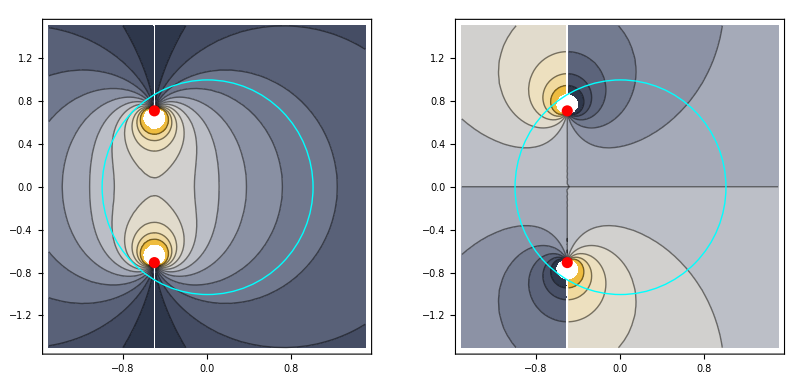

```mathematica
With[{z1=1/2 (-1-I Sqrt[2]),z2=1/2 (-1+I Sqrt[2])},GraphicsRow[Table[ContourPlot[g[1/Sqrt[4 (x+I y-z1) (x+I y-z2)]],{x,-1.5,1.5},{y,-1.5,1.5},ColorFunction->"GrayYellowTones",Epilog->{Cyan,Thick,Circle[{0,0}],Red,PointSize[0.02],Point[{Re@#,Im@#}&/@{z1,z2}]},Contours->11],{g,{Re,Im}}]]]
```

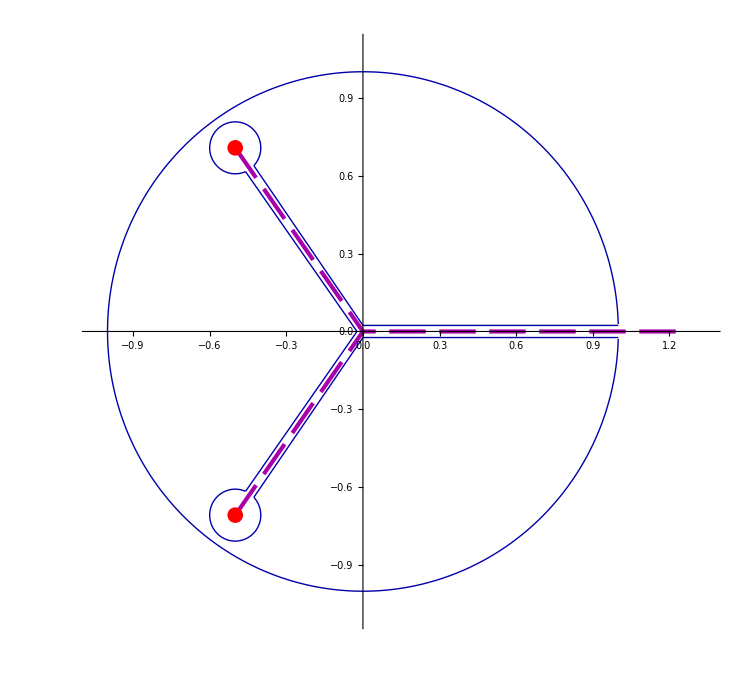

```mathematica
cp[{x_,y_},r_,t_,ϕ_,δ_]:=ConditionalExpression[{x,y}+r {Cos[t+ϕ],Sin[t+ϕ]},δ≤t≤2 Pi-δ]

Module[{z1=1/2 (-1-I Sqrt[2]),z2=1/2 (-1+I Sqrt[2]),z11,z22,r=1/10,δ,δ1},{z11,z22}={Re@#,Im@#}&/@{z1,z2};δ=2 r;δ1=δ/7;
ParametricPlot[{cp[{0,0},1,t,{0},δ1],cp[z11,r,t,-Pi+Arg[z1],δ],cp[z22,r,t,-Pi+Arg[z2],δ]},{t,0,2 Pi},PlotStyle->ConstantArray[{Thick,Darker@Blue},3],AxesStyle->Arrowheads[0.03],PlotRange->{{-1.05,1.35},{-1.1,1.1}},Epilog->{Darker@Blue,Thick,Line@{{cp[z11,r,δ,-Pi+Arg[z1],0],{Sin[Arg[z1]] δ1,0},cp[z22,r,2 Pi-δ,-Pi+Arg[z2],0]},{cp[z11,r,2 Pi-δ,-Pi+Arg[z1],0],{0,Sin[Arg[z1]] δ1},{1,Sin[Arg[z1]] δ1}},{cp[z22,r,δ,-Pi+Arg[z2],0],{0,-Sin[Arg[z1]] δ1},{1,-Sin[Arg[z1]] δ1}}},Darker@Magenta,Dashing[{0.035,0.013}],Thickness[0.004],Line@{{z11,{0,0},{1.25,0}},{z22,{0,0}}},Red,PointSize[0.015],Point[{z11,z22}]},ImageSize->750]]
```

```mathematica
With[{z1=1/2 (-1-I Sqrt[2]),z2=1/2 (-1+I Sqrt[2])},xLimit[{Integrate[(r I E^(I t))/(2 Sqrt[r E^(I t) (r E^(I t)+z1-z2)]),{t,0,2 Pi},Assumptions->r>0],Integrate[(r I E^(I t))/(2 Sqrt[r E^(I t) (r E^(I t)+z2-z1)]),{t,0,2 Pi},Assumptions->r>0]},r->0]]
```

xLimit[{ConditionalExpression[-2 ArcSinh[(√r)/2^(1/4)],r≤√2],ConditionalExpression[2 ArcSinh[(√r)/2^(1/4)],r≤√2]},r→0]

```mathematica
Integrate[( r E^(I t) )^n,{t,0,2 Pi},Assumptions->r>0]
Limit[%,n->1]
```

-(ⅈ (-1+ⅇ^(2 ⅈ n π)) r^n)/n

0

```mathematica
Integrate[1/(r Exp[I t]),r,t]
D[(r Exp[I t]),t]
```

ⅈ ⅇ^(-ⅈ t) Log[r]

ⅈ ⅇ^(ⅈ t) r

```mathematica
With[{z1=1/2 (-1-I Sqrt[2]),z2=1/2 (-1+I Sqrt[2])},{2 Integrate[z2/Sqrt[4 (t-1) z2 (t z2-z1)],{t,0,1}],-2 Integrate[z1/Sqrt[4 (t-1) z1 (t z1-z2)],{t,0,1}]}]
```

{1/2 ⅈ (2 π+ArcTan[(10 √2)/23]+2 ⅈ Log[Root[27+36 #1+116 #1^2+36 #1^3+27 #1^4&,2]]),-(2 ((2 ⅈ+√2) π+ArcCosh[7]+ⅈ √2 Log[2-√3]))/(-8+4 ⅈ √2)}

```mathematica
%//Simplify
```

{1/2 ⅈ (2 π+ArcTan[(10 √2)/23]+2 ⅈ Log[Root[27+36 #1+116 #1^2+36 #1^3+27 #1^4&,2]]),-(2 ((2 ⅈ+√2) π+ArcCosh[7]+ⅈ √2 Log[2-√3]))/(-8+4 ⅈ √2)}

```mathematica
FullSimplify[Plus@@With[{z1=1/2 (-1-I Sqrt[2]),z2=1/2 (-1+I Sqrt[2])},{2 Integrate[z2/Sqrt[4 (t-1) z2 (t z2-z1)],{t,0,1}],-2 Integrate[z1/Sqrt[4 (t-1) z1 (t z1-z2)],{t,0,1}]}]]
```

(ⅈ π)/2+(ⅈ ArcCosh[7]-√2 Log[2-√3])/(4 ⅈ+2 √2)+1/(-2 ⅈ+√2)(2 π+ArcTan[(10 √2)/23]+√2 Log[Root[1+4 #1^2+#1^4&,4]]+2 ⅈ Log[Root[27+36 #1+116 #1^2+36 #1^3+27 #1^4&,2]])

```mathematica
subL
```

{L_n_→∮_{z} [-(ⅈ z^(1+n) T[z])/(2 π)],Φ_n_→∮_{w} [-(ⅈ w^(-1+h+n) Φ[w])/(2 π)],T[z_].Φ[w_]→(h Φ[w])/(-w+z)^2+(UnderBar[∂]_w[Φ[w]])/(-w+z)}

```mathematica
PR[CO["4.4: BBS Problem 3.10:
(i) Show that in a unitary conformal field theory, that is, one with a positive-definite Hilbert space, BraKet[φ,φ]>0, the central charge satisfies c > 0, and the conformal dimensions of primary fields satisfy h ≥ 0. Hint: evaluate ",
$0=BraKet[φ,CommutatorM[Subscript[L, n],Subscript[L, -n]],φ]," for a highest-weight state |φ⟩.
(ii) Show that ",$h=h -> h̄ -> 0," if and only if ",$f=Ket[φ] ->Ket[0],"."]
];
subL={Limit[Subscript[Φ, j_][z_,_],z_->0]. Ket[0]->Ket[Subscript[Φ, j]],
Subscript[L, 0].Ket[Subscript[Φ, j_]]->Subscript[h, j] . Ket[Subscript[Φ, j]],Subscript[L, n_].Ket[Subscript[Φ, j_]]:>0/;n>0,deltaD[ff:(Subscript[Φ, j_][z_,z1_]),ϵ]->Subscript[h, j] xPartialD[ϵ[z],z]ff+ϵ[z] xPartialD[ff,z],
CommutatorM[Subscript[L, m_],Subscript[L, n_]]->(m-n)Subscript[L, m+n]+c/12(m^3-m)T[δ,"dd"][m+n,0]}/.Φ->ϕ/.Subscript[ϕ, j_]->ϕ^j;
PR["Using: ",subL[[-1]],
NL,"Evaluate As suggested: ",
Yield,$=$0->($0/.subL),
NL,"Expand ",
Yield,$=$//.BraKet[φ,a_+b_,φ]->Bra[φ].a.Ket[φ]+Bra[φ].b.Ket[φ]//.tuOpSimplify[Dot,{c,h,n,(-n_+n_^3)}],
NL,"Since: ",sub={Subscript[L, 0]. Ket[φ]->h Ket[φ],T[δ,"dd"][0,0].Ket[φ]->Ket[φ]},
Imply,$1=$=$/.sub/.tuOpSimplify[Dot,{c,h,n,(-n_+n_^3)}],
NL,"For primary field ",sub=n->1,
imply,Framed[($=$1/.sub)≥0],imply,h≥0,
NL,"•For the general case the Coefficient of ",sub=Bra[φ].Ket[φ]," needs to be ≥0 ",
Imply,Framed[$s=(ExtractPattern[$1,a_ sub][[1]]/.sub->1)>0],
NL,"So if c<0 and n->∞ the relationship >0 would not be satisfied.",imply,c>0,

New,"(ii) See if there is difference in ",$d=$f[[1]]-$f[[2]]," if ",subh=h->0,
NL,"Apply ",sub=Subscript[L, 0]," to ",$d,
imply,$=sub.#&/@$d//.simpleDot2[{}],
NL,"Since ",(sub={Subscript[L, 0].Ket[0]->0,Subscript[L, 0].Ket[φ]->h Ket[φ]})//Column,
imply,$=$->($/.sub),
NL,"If ",sub=h->0,
imply, $=$/.sub,
imply,$f," modulo L_0."
]
```

4.4: BBS Problem 3.10:
(i) Show that in a unitary conformal field theory, that is, one with a positive-definite Hilbert space, BraKet[φ,φ]>0, the central charge satisfies c > 0, and the conformal dimensions of primary fields satisfy h ≥ 0. Hint: evaluate ⟨φ|[L_n,L_-n]|φ⟩ for a highest-weight state |φ⟩.
(ii) Show that h→h̄→0 if and only if |φ⟩→|0⟩.

Using: [L_m_,L_n_]→(m-n) L_(m+n)+1/12 c (-m+m^3) δ_(m+n0)^(m+n0)
Evaluate As suggested: 
→ ⟨φ|[L_n,L_-n]|φ⟩→⟨φ|2 n L_0+1/12 c (-n+n^3) δ_00^00|φ⟩
Expand 
→ ⟨φ|[L_n,L_-n]|φ⟩→2 n ⟨φ|.L_0.|φ⟩+1/12 c (-n+n^3) ⟨φ|.δ_00^00.|φ⟩
Since: {L_0.|φ⟩→h |φ⟩,δ_00^00.|φ⟩→|φ⟩}
⇒ ⟨φ|[L_n,L_-n]|φ⟩→2 h n ⟨φ|.|φ⟩+1/12 c (-n+n^3) ⟨φ|.|φ⟩
For primary field n→1 ⇒ (⟨φ|[L_1,L_-1]|φ⟩→2 h ⟨φ|.|φ⟩)≥0 ⇒ h≥0
•For the general case the Coefficient of ⟨φ|.|φ⟩ needs to be ≥0 
⇒ (⟨φ|[L_n,L_-n]|φ⟩→2 h n+1/12 c (-n+n^3))>0
So if c<0 and n->∞ the relationship >0 would not be satisfied. ⇒ c>0
• (ii) See if there is difference in -|0⟩+|φ⟩ if h→0
Apply L_0 to -|0⟩+|φ⟩ ⇒ -L_0.|0⟩+L_0.|φ⟩
Since L_0.|0⟩→0
L_0.|φ⟩→h |φ⟩ ⇒ -L_0.|0⟩+L_0.|φ⟩→h |φ⟩
If h→0 ⇒ -L_0.|0⟩+L_0.|φ⟩→0 ⇒ |φ⟩→|0⟩ modulo L_0.

```mathematica
PR["Check OPE algorithm with Wray: ",
$=$0=OPE[T[z]·T[z1]];$//Framed,
NL,"where ",$s={T[z_]->NormalOrder[{tuDPartial[X[z],z],tuDPartial[X[z],z]}]/2,NormalOrder[{a_ , b_}]:>RadialOrder[a ·(b/.zz:z|z1->w[zz])]+OPE[a·(b/.zz:z|z1->w[zz])],
w[z]->w,w[z1]->w1(*,
OPE[tuDPartial[X[z_],z_]·tuDPartial[X[w_],w_]]->-1/4/(z-w)^2*)
};$s//Column,
NL,"Compute Wick theorem template: ",
$=NormalOrder[xProduct[Subscript[ϕ, i],{i,k1}]]·NormalOrder[xProduct[Subscript[ψ, i],{i,k2}]];
$=$/.k1->2/.k2->2//tuProductExpand[List];
$2=$//tuOPEWick;$2//ColumnSumExp,

Yield,$0=$0/.$s//.tuOpSimplify[CenterDot],
NL,"Build dictionary:",
$pos=$0//tuExtractPositionPattern[CenterDot[_,_]]//First,
Yield,$=$pos[[2]]/.NormalOrder[a_]->a,CK,
Yield,$s={Subscript[ϕ, 1]->$[[1,1]],Subscript[ϕ, 2]->$[[1,2]],Subscript[ψ, 1]->$[[2,1]],Subscript[ψ, 2]->$[[2,2]]},
$=$2/.$s;
$pos[[2]]=$;
Yield,$=tuReplacePart[$0,{$pos}];$[[1]]//Expand//Framed

];
```

Check OPE algorithm with Wray: OPE[T[z]·T[z1]]
where T[z_]→1/2 NormalOrder[{UnderBar[∂]_z[X[z]],UnderBar[∂]_z[X[z]]}]
NormalOrder[{a_,b_}]:>RadialOrder[a·(b/.zz:z|z1→w[zz])]+OPE[a·(b/.zz:z|z1→w[zz])]
w[z]→w
w[z1]→w1
Compute Wick theorem template: ∑[⟨ϕ_1|ψ_2⟩ ⟨ϕ_2|ψ_1⟩
⟨ϕ_1|ψ_1⟩ ⟨ϕ_2|ψ_2⟩
⟨ϕ_2|ψ_2⟩ NormalOrder[{ϕ_1,ψ_1}]
⟨ϕ_2|ψ_1⟩ NormalOrder[{ϕ_1,ψ_2}]
⟨ϕ_1|ψ_2⟩ NormalOrder[{ϕ_2,ψ_1}]
⟨ϕ_1|ψ_1⟩ NormalOrder[{ϕ_2,ψ_2}]
NormalOrder[{ϕ_1,ϕ_2,ψ_1,ψ_2}]]
→ OPE[1/4 NormalOrder[{UnderBar[∂]_z[X[z]],UnderBar[∂]_z[X[z]]}]·NormalOrder[{UnderBar[∂]_z1[X[z1]],UnderBar[∂]_z1[X[z1]]}]]
Build dictionary:{1,2}→NormalOrder[{UnderBar[∂]_z[X[z]],UnderBar[∂]_z[X[z]]}]·NormalOrder[{UnderBar[∂]_z1[X[z1]],UnderBar[∂]_z1[X[z1]]}]
→ {UnderBar[∂]_z[X[z]],UnderBar[∂]_z[X[z]]}·{UnderBar[∂]_z1[X[z1]],UnderBar[∂]_z1[X[z1]]}⟵CHECK
→ {ϕ_1→UnderBar[∂]_z[X[z]],ϕ_2→UnderBar[∂]_z[X[z]],ψ_1→UnderBar[∂]_z1[X[z1]],ψ_2→UnderBar[∂]_z1[X[z1]]}
→ 1/2 ⟨UnderBar[∂]_z[X[z]]|UnderBar[∂]_z1[X[z1]]⟩^2+⟨UnderBar[∂]_z[X[z]]|UnderBar[∂]_z1[X[z1]]⟩ NormalOrder[{UnderBar[∂]_z[X[z]],UnderBar[∂]_z1[X[z1]]}]+1/4 NormalOrder[{UnderBar[∂]_z[X[z]],UnderBar[∂]_z[X[z]],UnderBar[∂]_z1[X[z1]],UnderBar[∂]_z1[X[z1]]}]

```mathematica
Clear[tuProductExpand]
tuProductExpand::usage="tuProductExpand[op_:Times][exp_] expands Product|xProduct operations in exp_ with op_ as product operator. This routine needs Numerical range of productOp[_,{i,9}]. *30Oct2015*";
tuProductExpand[op_:Times][exp_]:=Block[{$=exp,productOp=Product|xProduct},
$=$/.(pp:productOp)[a_,b__]:>op@@Table[a,b]
];

Clear[OPEContract]
OPEContract::usage="OPEContract[e1_,e2_] performs OPE contraction product of two NormalOrder[]d operators. BraKet indicates contraction. *30Oct2015*";
OPEContract[e1_,e2_]:=Block[{$,$1=List@@e1,$2=List@@e2},
$=Map[(BraKet@@# )NormalOrder[Complement[$1,#]]·NormalOrder[Complement[$2,#]]&,Tuples[{$1,$2}]];
Apply[Plus,$]
];
tuOPEWick::usage="tuOPEWick[exp_] applies Wick's Theorem for OPE on exp_.  Only does 2 levels of nesting *30Oct2015*";
tuOPEWick[exp_]:=Block[{$=exp,$sNO},
$sNO=NormalOrder[a_List]·NormalOrder[b_List]:>NormalOrder[Join[a,b]]+xOPEContract[a,b];
$=$/.$sNO;
$=$/.xOPEContract->OPEContract;xPrint[$];
$=$/.$sNO;
$=$/.xOPEContract[a__]->(1/2)OPEContract[a]/.NormalOrder[{}]->1//Expand//(#//.tuOpSimplify[CenterDot])&;
$
];

$=NormalOrder[xProduct[Subscript[ϕ, i],{i,k1}]]·NormalOrder[xProduct[Subscript[ψ, i],{i,k2}]];
$=$/.k1->2/.k2->2//tuProductExpand[List]
$=$//tuOPEWick
$=$/.$s;$//ColumnSumExp
```

NormalOrder[{ϕ_1,ϕ_2}]·NormalOrder[{ψ_1,ψ_2}]

⟨ϕ_1|ψ_2⟩ ⟨ϕ_2|ψ_1⟩+⟨ϕ_1|ψ_1⟩ ⟨ϕ_2|ψ_2⟩+⟨ϕ_2|ψ_2⟩ NormalOrder[{ϕ_1,ψ_1}]+⟨ϕ_2|ψ_1⟩ NormalOrder[{ϕ_1,ψ_2}]+⟨ϕ_1|ψ_2⟩ NormalOrder[{ϕ_2,ψ_1}]+⟨ϕ_1|ψ_1⟩ NormalOrder[{ϕ_2,ψ_2}]+NormalOrder[{ϕ_1,ϕ_2,ψ_1,ψ_2}]

∑[2 ⟨UnderBar[∂]_z[X[z]]|UnderBar[∂]_z1[X[z1]]⟩^2
4 ⟨UnderBar[∂]_z[X[z]]|UnderBar[∂]_z1[X[z1]]⟩ NormalOrder[{UnderBar[∂]_z[X[z]],UnderBar[∂]_z1[X[z1]]}]
NormalOrder[{UnderBar[∂]_z[X[z]],UnderBar[∂]_z[X[z]],UnderBar[∂]_z1[X[z1]],UnderBar[∂]_z1[X[z1]]}]]

```mathematica
PR[CO["Verify the expression (3.78) for the central charge of a system of b, c ghosts by computing the OPE of the energy-momentum tensor ",T[T,"dd"][b,c]," with itself."]
];
PR["■Show Conformal anomaly(3.78): ",$e378=c[ℯ,λ]->-2 ℯ(6 λ^2-6λ+1),
NL,"•The energy-momentum tensor(3.77): ",$e377=Subscript[T, bc][z_]->-λ NormalOrder[{b[z],tuDPartial[c[z],z]}]+ℯ(λ-1) NormalOrder[{c[z],tuDPartial[b[z],z]}],
NL,"Use: ",$sNO=NormalOrder[a_,b_]:>RadialOrder[a ·(b/.z->w[z])]+OPE[a·(b/.z->w[z])];$sNO//Framed,
Imply,$=$e377a=$e377/.$sNO;$//ColumnSumExp,
NL,"•Compute:",
yield,$=$00=OPE[Subscript[T, bc][z]·Subscript[T, bc][z1]];$//Framed,"POFF",
Yield,$=$/.$e377,
Yield,$0=$/.tuOpDistribute[CenterDot]//.tuOpSimplify[CenterDot,{λ,ℯ}]//Simplify,
line,
NL,"●Build Wick theorem template: ",
$=NormalOrder[xProduct[Subscript[ϕ, i],{i,k1}]]·NormalOrder[xProduct[Subscript[ψ, i],{i,k2}]];
$s0=$=$/.k1->2/.k2->2//tuProductExpand[List];
Yield,$wtmp=$=$s0->($//tuOPEWick)/.{Subscript[ϕ, 1]->a,Subscript[ϕ, 2]->b,Subscript[ψ, 1]->c,Subscript[ψ, 2]->d}//tuAddPatternVariable[{a,b,c,d}];$//ColumnSumExp,
line,
$=$0/.$wtmp//Simplify,
NL,"Contraction of the same field → 0: ",
$s={BraKet[a1_,a2_]:>0/;(!FreeQ[a1,b]&&!FreeQ[a2,b])||(!FreeQ[a1,c]&&!FreeQ[a2,c])},
Yield,$=$/.$s//Expand,"PON",
NL,"Order terms with tuDPartial last: ",$s={(op:NormalOrder)[{aa:tuDPartial[_,_],bb_}]:>-op[{bb,aa}]/;FreeQ[bb,tuDPartial[_,_]],
(op:BraKet)[aa:tuDPartial[_,_],bb_]:>-op[bb,aa]/;FreeQ[bb,tuDPartial[_,_]]}
,
line,
Yield,$=$//.$s//ExpandAll;$//ColumnSumExp,
NL,"The c-term comes from the completely contracted term of (3.37): ",
$e337=OPE[T[z]·T[w]]->c/2 1/(z-w)^4+2/(z-w)^2 T[w]+1/(z-w)tuDPartial[T[w],w],
NL,"The corresponding term is: ",
xtmp=$=$/.NormalOrder[_]->0//First
];
$=xtmp//Simplify;$//ColumnSumExp
$s={BraKet[c[z_],b[w_]]->1/(z-w),BraKet[b[z_],c[w_]]->ℯ/(z-w),BraKet[b[z_],tuDPartial[c[w_],w_]]:>tuDPartial[ℯ/(z-w),w],BraKet[c[z_],tuDPartial[b[w_],w_]]:>tuDPartial[1/(z-w),w],
BraKet[tuDPartial[c[z_],z_],tuDPartial[b[w_],w_]]:>tuDPartial[tuDPartial[1/(z-w),w],z],
BraKet[tuDPartial[b[z_],z_],tuDPartial[c[w_],w_]]:>tuDPartial[tuDPartial[ℯ/(z-w),w],z]}
$=$/.$s
$=$//tuDerivOps2D//Simplify
```

Verify the expression (3.78) for the central charge of a system of b, c ghosts by computing the OPE of the energy-momentum tensor T_bc^bc with itself.

■Show Conformal anomaly(3.78): c[ℯ,λ]→-2 ℯ (1-6 λ+6 λ^2)
•The energy-momentum tensor(3.77): T_bc[z_]→-λ NormalOrder[{b[z],UnderBar[∂]_z[c[z]]}]+ℯ (-1+λ) NormalOrder[{c[z],UnderBar[∂]_z[b[z]]}]
Use: NormalOrder[a_,b_]:>RadialOrder[a·(b/.z→w[z])]+OPE[a·(b/.z→w[z])]
⇒ T_bc[z_]→∑[-λ NormalOrder[{b[z],UnderBar[∂]_z[c[z]]}]
ℯ (-1+λ) NormalOrder[{c[z],UnderBar[∂]_z[b[z]]}]]
•Compute: ⟶ OPE[T_bc[z]·T_bc[z1]]
Order terms with tuDPartial last: {(op:NormalOrder)[{aa:UnderBar[∂]__[_],bb_}]:>-op[{bb,aa}]/;FreeQ[bb,tuDPartial[_,_]],(op:BraKet)[aa:UnderBar[∂]__[_],bb_]:>-op[bb,aa]/;FreeQ[bb,tuDPartial[_,_]]}
————————————————————————————————————————————————————————————
→ OPE[∑[-λ^2 ⟨b[z]|UnderBar[∂]_z1[c[z1]]⟩ ⟨b[z1]|UnderBar[∂]_z[c[z]]⟩
-ℯ^2 ⟨c[z]|UnderBar[∂]_z1[b[z1]]⟩ ⟨c[z1]|UnderBar[∂]_z[b[z]]⟩
2 ℯ^2 λ ⟨c[z]|UnderBar[∂]_z1[b[z1]]⟩ ⟨c[z1]|UnderBar[∂]_z[b[z]]⟩
-ℯ^2 λ^2 ⟨c[z]|UnderBar[∂]_z1[b[z1]]⟩ ⟨c[z1]|UnderBar[∂]_z[b[z]]⟩
ℯ λ ⟨c[z]|b[z1]⟩ ⟨UnderBar[∂]_z[b[z]]|UnderBar[∂]_z1[c[z1]]⟩
-ℯ λ^2 ⟨c[z]|b[z1]⟩ ⟨UnderBar[∂]_z[b[z]]|UnderBar[∂]_z1[c[z1]]⟩
ℯ λ ⟨b[z]|c[z1]⟩ ⟨UnderBar[∂]_z[c[z]]|UnderBar[∂]_z1[b[z1]]⟩
-ℯ λ^2 ⟨b[z]|c[z1]⟩ ⟨UnderBar[∂]_z[c[z]]|UnderBar[∂]_z1[b[z1]]⟩
ℯ λ ⟨UnderBar[∂]_z[c[z]]|UnderBar[∂]_z1[b[z1]]⟩ NormalOrder[{b[z],c[z1]}]
-ℯ λ^2 ⟨UnderBar[∂]_z[c[z]]|UnderBar[∂]_z1[b[z1]]⟩ NormalOrder[{b[z],c[z1]}]
-λ^2 ⟨b[z1]|UnderBar[∂]_z[c[z]]⟩ NormalOrder[{b[z],UnderBar[∂]_z1[c[z1]]}]
-λ^2 ⟨b[z]|UnderBar[∂]_z1[c[z1]]⟩ NormalOrder[{b[z1],UnderBar[∂]_z[c[z]]}]
ℯ λ ⟨UnderBar[∂]_z[b[z]]|UnderBar[∂]_z1[c[z1]]⟩ NormalOrder[{c[z],b[z1]}]
-ℯ λ^2 ⟨UnderBar[∂]_z[b[z]]|UnderBar[∂]_z1[c[z1]]⟩ NormalOrder[{c[z],b[z1]}]
-ℯ^2 ⟨c[z1]|UnderBar[∂]_z[b[z]]⟩ NormalOrder[{c[z],UnderBar[∂]_z1[b[z1]]}]
2 ℯ^2 λ ⟨c[z1]|UnderBar[∂]_z[b[z]]⟩ NormalOrder[{c[z],UnderBar[∂]_z1[b[z1]]}]
-ℯ^2 λ^2 ⟨c[z1]|UnderBar[∂]_z[b[z]]⟩ NormalOrder[{c[z],UnderBar[∂]_z1[b[z1]]}]
-ℯ^2 ⟨c[z]|UnderBar[∂]_z1[b[z1]]⟩ NormalOrder[{c[z1],UnderBar[∂]_z[b[z]]}]
2 ℯ^2 λ ⟨c[z]|UnderBar[∂]_z1[b[z1]]⟩ NormalOrder[{c[z1],UnderBar[∂]_z[b[z]]}]
-ℯ^2 λ^2 ⟨c[z]|UnderBar[∂]_z1[b[z1]]⟩ NormalOrder[{c[z1],UnderBar[∂]_z[b[z]]}]
ℯ λ ⟨c[z]|b[z1]⟩ NormalOrder[{UnderBar[∂]_z[b[z]],UnderBar[∂]_z1[c[z1]]}]
-ℯ λ^2 ⟨c[z]|b[z1]⟩ NormalOrder[{UnderBar[∂]_z[b[z]],UnderBar[∂]_z1[c[z1]]}]
ℯ λ ⟨b[z]|c[z1]⟩ NormalOrder[{UnderBar[∂]_z[c[z]],UnderBar[∂]_z1[b[z1]]}]
-ℯ λ^2 ⟨b[z]|c[z1]⟩ NormalOrder[{UnderBar[∂]_z[c[z]],UnderBar[∂]_z1[b[z1]]}]
λ^2 NormalOrder[{b[z],UnderBar[∂]_z[c[z]],b[z1],UnderBar[∂]_z1[c[z1]]}]
ℯ λ NormalOrder[{b[z],UnderBar[∂]_z[c[z]],c[z1],UnderBar[∂]_z1[b[z1]]}]
-ℯ λ^2 NormalOrder[{b[z],UnderBar[∂]_z[c[z]],c[z1],UnderBar[∂]_z1[b[z1]]}]
ℯ λ NormalOrder[{c[z],UnderBar[∂]_z[b[z]],b[z1],UnderBar[∂]_z1[c[z1]]}]
-ℯ λ^2 NormalOrder[{c[z],UnderBar[∂]_z[b[z]],b[z1],UnderBar[∂]_z1[c[z1]]}]
ℯ^2 NormalOrder[{c[z],UnderBar[∂]_z[b[z]],c[z1],UnderBar[∂]_z1[b[z1]]}]
-2 ℯ^2 λ NormalOrder[{c[z],UnderBar[∂]_z[b[z]],c[z1],UnderBar[∂]_z1[b[z1]]}]
ℯ^2 λ^2 NormalOrder[{c[z],UnderBar[∂]_z[b[z]],c[z1],UnderBar[∂]_z1[b[z1]]}]]]
The c-term comes from the completely contracted term of (3.37): OPE[T[z]·T[w]]→c/(2 (-w+z)^4)+(2 T[w])/(-w+z)^2+(UnderBar[∂]_w[T[w]])/(-w+z)
The corresponding term is: -λ^2 ⟨b[z]|UnderBar[∂]_z1[c[z1]]⟩ ⟨b[z1]|UnderBar[∂]_z[c[z]]⟩-ℯ^2 ⟨c[z]|UnderBar[∂]_z1[b[z1]]⟩ ⟨c[z1]|UnderBar[∂]_z[b[z]]⟩+2 ℯ^2 λ ⟨c[z]|UnderBar[∂]_z1[b[z1]]⟩ ⟨c[z1]|UnderBar[∂]_z[b[z]]⟩-ℯ^2 λ^2 ⟨c[z]|UnderBar[∂]_z1[b[z1]]⟩ ⟨c[z1]|UnderBar[∂]_z[b[z]]⟩+ℯ λ ⟨c[z]|b[z1]⟩ ⟨UnderBar[∂]_z[b[z]]|UnderBar[∂]_z1[c[z1]]⟩-ℯ λ^2 ⟨c[z]|b[z1]⟩ ⟨UnderBar[∂]_z[b[z]]|UnderBar[∂]_z1[c[z1]]⟩+ℯ λ ⟨b[z]|c[z1]⟩ ⟨UnderBar[∂]_z[c[z]]|UnderBar[∂]_z1[b[z1]]⟩-ℯ λ^2 ⟨b[z]|c[z1]⟩ ⟨UnderBar[∂]_z[c[z]]|UnderBar[∂]_z1[b[z1]]⟩

∑[-λ^2 ⟨b[z]|UnderBar[∂]_z1[c[z1]]⟩ ⟨b[z1]|UnderBar[∂]_z[c[z]]⟩
-ℯ (-1+λ) (ℯ (-1+λ) ⟨c[z]|UnderBar[∂]_z1[b[z1]]⟩ ⟨c[z1]|UnderBar[∂]_z[b[z]]⟩+λ (⟨c[z]|b[z1]⟩ ⟨UnderBar[∂]_z[b[z]]|UnderBar[∂]_z1[c[z1]]⟩+⟨b[z]|c[z1]⟩ ⟨UnderBar[∂]_z[c[z]]|UnderBar[∂]_z1[b[z1]]⟩))]

{⟨c[z_]|b[w_]⟩→1/(-w+z),⟨b[z_]|c[w_]⟩→ℯ/(-w+z),⟨b[z_]|UnderBar[∂]_w_[c[w_]]⟩:>tuDPartial[ℯ/(z-w),w],⟨c[z_]|UnderBar[∂]_w_[b[w_]]⟩:>tuDPartial[1/(z-w),w],⟨UnderBar[∂]_z_[c[z_]]|UnderBar[∂]_w_[b[w_]]⟩:>tuDPartial[tuDPartial[1/(z-w),w],z],⟨UnderBar[∂]_z_[b[z_]]|UnderBar[∂]_w_[c[w_]]⟩:>tuDPartial[tuDPartial[ℯ/(z-w),w],z]}

-λ^2 UnderBar[∂]_z1[ℯ/(z-z1)] UnderBar[∂]_z[ℯ/(-z+z1)]-ℯ (-1+λ) (ℯ (-1+λ) UnderBar[∂]_z1[1/(z-z1)] UnderBar[∂]_z[1/(-z+z1)]+λ ((ℯ UnderBar[∂]_z[UnderBar[∂]_z1[1/(z-z1)]])/(z-z1)+(UnderBar[∂]_z[UnderBar[∂]_z1[ℯ/(z-z1)]])/(z-z1)))

(ℯ^2 (-1-2 λ+2 λ^2))/(z-z1)^4

```mathematica
CommutatorM[Q.Q,b]->CommutatorM[Q,CommutatorP[Q,b]]
%/.CommutatorM->MCommutator/.CommutatorP->ACommutator//.Dot->CenterDot//.tuOpDistribute[CenterDot]//.tuOpSimplify[CenterDot]/.Rule->Equal
```

[Q.Q,b]→[Q,{Q,b}]

True

```mathematica
Clear[tuExtractIntegrand]
tuExtractIntegrand[exp_]:=Block[{pos,tmp},
tmp=tuExtractPositionPattern[IntegralOp[a_,b_]|tuIntegral[a_,b_]|xIntegral[a_,b__]][exp]//First;
If[FreeQ[tmp,Integrate],
{   Append[First[tmp],2]->tmp[[2,2]] },
{   Append[First[tmp],1]->tmp[[2,1]] }
]//First
];

$e435
%//tuExtractIntegrand
```

S→-((-(B_μ^μ·B_μ^μ)+UnderBar[∂]_α[X_μ^μ]·UnderBar[∂]^α[X_μ^μ]+(ψ̄)_μ^μ·ρ_α^α·UnderBar[∂]_α[ψ_μ^μ])σσ)/(2 π)

{2,3,1}→-(B_μ^μ·B_μ^μ)+UnderBar[∂]_α[X_μ^μ]·UnderBar[∂]^α[X_μ^μ]+(ψ̄)_μ^μ·ρ_α^α·UnderBar[∂]_α[ψ_μ^μ]

```mathematica
Select[xtmp,!FreeQ[#,X]&]//ColumnSumExp
```

∑[ϵ̄·UnderBar[∂]_α[ψ_μ^μ]·UnderBar[∂]^α[X_μ^μ]
UnderBar[∂]_α[X_μ^μ]·ϵ̄·UnderBar[∂]^α[ψ_μ^μ]
(ψ̄)_μ^μ·ρ_α^α·ρ_α2^α2·UnderBar[∂]_α[UnderBar[∂]_α2[X_μ^μ]]·ϵ
δ[(ψ̄)_μ^μ]·ρ_α^α·ρ_α2^α2·UnderBar[∂]_α[UnderBar[∂]_α2[X_μ^μ]]·ϵ]

```mathematica
$s1=δ[T[ψ̄,"u"][μ]]
$=$s1/.$e425//tudExpand[δ,{β}]//(#//.tuOpSimplify[CenterDot]/.$e425[[1;;3]])&
$s1=$s1->$
$e425a={$s1,$e425}//Flatten

$=Table[T[ρ,"u"][i].T[ρ,"u"][j] fn[i,j],{i,0,1},{j,0,1}]//Flatten
$=$/.$e425a/.fn[1,0]->fn[0,1];$//MatrixForms
Apply[Plus,$]//MatrixForms
```

δ[(ψ̄)_μ^μ]

((B_μ^μ·ϵ)^†+(ρ_α^α·UnderBar[∂]_α[X_μ^μ]·ϵ)^†)·β

δ[(ψ̄)_μ^μ]→((B_μ^μ·ϵ)^†+(ρ_α^α·UnderBar[∂]_α[X_μ^μ]·ϵ)^†)·β

{δ[(ψ̄)_μ^μ]→((B_μ^μ·ϵ)^†+(ρ_α^α·UnderBar[∂]_α[X_μ^μ]·ϵ)^†)·β,δ[X_μ^μ]→ϵ̄·ψ_μ^μ,δ[ψ_μ^μ]→B_μ^μ·ϵ+ρ_α^α·UnderBar[∂]_α[X_μ^μ]·ϵ,δ[B_μ^μ]→ϵ̄·ρ_α^α·UnderBar[∂]_α[ψ_μ^μ],Tensor[OverBar[ψ_],uu_,dd_]→Tensor[ψ,uu,dd]^†·β,ϵ̄→ϵ^†·β,β→ⅈ ρ_0^0,ρ_0^0→{{0,-1},{1,0}},ρ_1^1→{{0,1},{1,0}}}

{ρ_0^0.ρ_0^0 fn[0,0],ρ_0^0.ρ_1^1 fn[0,1],ρ_1^1.ρ_0^0 fn[1,0],ρ_1^1.ρ_1^1 fn[1,1]}

((-fn[0,0] | 0
0 | -fn[0,0])
(-fn[0,1] | 0
0 | fn[0,1])
(fn[0,1] | 0
0 | -fn[0,1])
(fn[1,1] | 0
0 | fn[1,1]))

(-fn[0,0]+fn[1,1] | 0
0 | -fn[0,0]+fn[1,1])

```mathematica
Clear[tuScalarSelect]
tuScalarSelect::usage="tuScalarSelect[scalars_List:{}][exp_] returns a List of NumericQ[] and scalars_ in exp_. *12Nov2015*";
tuScalarSelect[scalars_List:{}][exp_]:=Block[{$=exp,$pos},
$pos=$//tuExtractPositionPattern[{_?NumericQ,scalars}];
$=Map[#[[2]]&,$pos]
];
(**)
Clear[tuScalarDelete]
tuScalarDelete::usage="tuScalarDelete[scalars_List:{}][exp_] returns exp_ with NumericQ[] and scalars_ in removed. *12Nov2015*";
tuScalarDelete[scalars_List:{}][exp_]:=Block[{$=exp,$pos},
$pos=$//tuExtractPositionPattern[{_?NumericQ,scalars}];
$pos=Map[#[[1]]&,$pos];
$=Delete[$,$pos];
$
];

xtmp//tuDerivativeExpand[]
1//tuScalarDelete[]
```

{{-ⅈ UnderBar[∂]_(θ_+^+)[ARG],ⅈ UnderBar[∂]_(θ_-^-)[ARG]}}

Sequence[]

```mathematica
e47
$p2

//FullForm
$=xtmp/.ss:OverBar[$se[[1]]]:>(ss//.e47/.$se//tuConjugateTransposeSimplify[{Tensor[ε,_,_]}]);
$=$/.CenterDot->ncDot/.dd:ncDot[__]:>NonCommutativeDot[dd]  //.tuOpDistribute[Dot]//.tuOpSimplify[Dot]//.{{a_}}->a//tuRepeat[{tuOpDistribute[Dot],tuOpSimplify[Dot],tt:Tensor[θ,_,_].Tensor[ε,_,_]:>-Reverse[tt]},Expand];
$//ColumnSumExp
```

{OverBar[T_]→T^†.β,β→ⅈ ρ_0^0,ρ_0^0→{{0,-1},{1,0}},ρ_1^1→{{0,1},{1,0}},ρ_0^0→{{0,1},{-1,0}},ρ_1^1→{{0,1},{1,0}}}

UnderBar[∂]_OverBar[θ_A^A][ARG]→{{-ⅈ UnderBar[∂]_(θ_+^+)[ARG],ⅈ UnderBar[∂]_(θ_-^-)[ARG]}}

```mathematica
$L0
```

ℒ→OverBar[ψ_μ^μ].ρ_α^α.UnderBar[∂]_α[ψ_μ^μ]+UnderBar[∂]_α[X_μ^μ] UnderBar[∂]^α[X_μ^μ]

```mathematica
e468
e469
e470
e456
```

L_m_^m_→(∫_{σ,-π,π} [ⅇ^(ⅈ m σ) T_(++)])/π→(L^b)_m^m+(L^f)_m^m

(L^b)_m^m→1/2 UnderBar[∑]_{n∈ℤ}[NormalOrder[α_-n^-n.α_(m+n)^(m+n)]]

(L^f)_m^m→1/2 UnderBar[∑]_{r∈{1/2+ℤ}}[(m/2+r) NormalOrder[b_-r^-r.b_(m+r)^(m+r)]]

(ψ_+)_μ^μ→(UnderBar[∑]_{r∈{1/2+ℤ}}[ⅇ^(-ⅈ r (σ+τ)) b_rμ^rμ])/(√2)

L_m^m→(L^b)_m^m+(L^f)_m^m

```mathematica
$1=$/.xSum[a_,b_]:> xSum[a+(a/.r->-r),{r∈{ℤ+1/2>0}}]//Simplify

$s=CommutatorP[T[b,"du"][r1,μ1],T[b,"dd"][r2,μ2]]->T[η,"ud"][μ1,μ2]T[δ,"dd"][r1+r2,0]/.CommutatorP->ACommutator

$s=tuRuleSolve[$s,$s[[1,2]]]/.r1->r/.r2->-r//tuAddPatternVariable[{μ1,μ2}]
$1/.$s//Simplify
```

{[α_mμ^mμ,α_nν^nν]→m δ_(m+n0)^(m+n0) η_μν^μν,{b_rμ^rμ,b_sν^sν}→δ_(r+s0)^(r+s0) η_μν^μν,{d_mμ^mμ,d_nν^nν}→δ_(m+n0)^(m+n0) η_μν^μν}

b_r2μ2^r2μ2.b_r1μ1^r1μ1+b_r1μ1^r1μ1.b_r2μ2^r2μ2→δ_(r1+r20)^(r1+r20) η_μ1μ2^μ1μ2

{b_rμ1_^rμ1_.b_-rμ2_^-rμ2_→-b_-rμ2^-rμ2.b_rμ1^rμ1+δ_00^00 η_μ1μ2^μ1μ2}

{[α_mμ^mμ,α_nν^nν]→m δ_(m+n0)^(m+n0) η_μν^μν,{b_rμ^rμ,b_sν^sν}→δ_(r+s0)^(r+s0) η_μν^μν,{d_mμ^mμ,d_nν^nν}→δ_(m+n0)^(m+n0) η_μν^μν}

```mathematica
PR["•R-sector (4.72): ",$e472R,
Yield,$=$e485[[-1]],
Yield,$=$//.$e472R,
NL,"The commutation relations: ",$s=$e461,
NL,"For: ",$s1={Tensor[η,_,_]->dim-2,m->-n,r->-s,T[δ,"dd"][0,0]->1},
Yield,$s=$s//tuIndexDeleteAll[{μ,ν}]//(#//.$s1)&;$s//Column,
yield,"Expand: ",$sc=$s/.CommutatorM->MCommutator/.CommutatorP->ACommutator;$s=$sc[[{1,3}]];
yield,$v={T[α,"d"][-n].T[α,"d"][n],T[d,{},{-n}].T[d,{},{n}]};
yield,$s=tuRuleSolve[$s,$v];$s//Column,
Imply,$=$/.$s/.tuOpDistribute[xSum]/.tuOpDistribute[Dot]/.tuOpSwitch[Dot,xSum]//.tuOpSimplify[Dot,{n}],
NL,"For physical ground state require ",$s={Dot[T[α|d,{},{-n}],Ket[ϕ]]->0},
Yield,$=$/.$s//.tuOpSimplify[Dot,{dim}]//tuOpSimplifyFirst[xSum]
]
```

•R-sector (4.72): {L_0^0→N+1/2 (α_0^0)^2,N→UnderBar[∑]_{n,1,∞}[n d_-n^-n.d_n^n]+UnderBar[∑]_{n,1,∞}[α_-n^-n.α_n^n]}
→ (-a_R+L_0^0).|ϕ⟩→0
→ (-a_R+1/2 (α_0^0)^2+UnderBar[∑]_{n,1,∞}[n d_-n^-n.d_n^n]+UnderBar[∑]_{n,1,∞}[α_-n^-n.α_n^n]).|ϕ⟩→0
The commutation relations: {[α_mμ^mμ,α_nν^nν]→m δ_(m+n0)^(m+n0) η_μν^μν,{b_rμ^rμ,b_sν^sν}→δ_(r+s0)^(r+s0) η_μν^μν,{d_mμ^mμ,d_nν^nν}→δ_(m+n0)^(m+n0) η_μν^μν}
For: {Tensor[η,_,_]→-2+dim,m→-n,r→-s,δ_00^00→1}
→ [α_-n^-n,α_n^n]→-(-2+dim) n
{b_-s^-s,b_s^s}→-2+dim
{d_-n^-n,d_n^n}→-2+dim ⟶ Expand:  ⟶  ⟶ α_-n^-n.α_n^n→2 n-dim n+α_n^n.α_-n^-n
d_-n^-n.d_n^n→-2+dim-d_n^n.d_-n^-n
⇒ -a_R.|ϕ⟩+1/2 (α_0^0)^2.|ϕ⟩+UnderBar[∑]_{n,1,∞}[-n dim.|ϕ⟩]+UnderBar[∑]_{n,1,∞}[n dim.|ϕ⟩]+UnderBar[∑]_{n,1,∞}[-n d_n^n.d_-n^-n.|ϕ⟩]+UnderBar[∑]_{n,1,∞}[α_n^n.α_-n^-n.|ϕ⟩]+UnderBar[∑]_{n,1,∞}[-2 n |ϕ⟩]+UnderBar[∑]_{n,1,∞}[2 n |ϕ⟩]→0
For physical ground state require {((α|d)_-n^-n).|ϕ⟩→0}
→ -a_R.|ϕ⟩+1/2 (α_0^0)^2.|ϕ⟩+2 UnderBar[∑]_{n,1,∞}[0]→0

```mathematica
PR["For the NS-sector: ",
NL,"(4.70) for m→0 ",imply,$s=tuRuleSelect[$e479][T[L^f,"d"][m]]/.m->0,
Yield,$s=$s/.xSum[a_,b_]:>xSum[(a/.NormalOrder[c_]->c),b>0]+xSum[(a/.r->-r),b>0],
Yield,$s=$s/.NormalOrder[a_]:>(-Reverse[a]),

Imply,e468[[1]]->e468[[2,2]]/.$s,CK,
Yield,$=$e48[[-1]],
Yield,$=$//.$e472R,
NL,"The commutation relations: ",$s=$e461,
NL,"For: ",$s1={Tensor[η,_,_]->dim-2,m->-n,r->-s,T[δ,"dd"][0,0]->1},
Yield,$s=$s//tuIndexDeleteAll[{μ,ν}]//(#//.$s1)&;$s//Column,
yield,"Expand: ",$sc=$s/.CommutatorM->MCommutator/.CommutatorP->ACommutator;$s=$sc[[{1,3}]];
yield,$v={T[α,"d"][-n].T[α,"d"][n],T[d,{},{-n}].T[d,{},{n}]};
yield,$s=tuRuleSolve[$s,$v];$s//Column,
Imply,$=$/.$s/.tuOpDistribute[xSum]/.tuOpDistribute[Dot]/.tuOpSwitch[Dot,xSum]//.tuOpSimplify[Dot,{n}],
NL,"For physical ground state require ",$s={Dot[T[α|d,{},{-n}],Ket[ϕ]]->0},
Yield,$=$/.$s//.tuOpSimplify[Dot,{dim}]//tuOpSimplifyFirst[xSum]
]
```

For the NS-sector: 
(4.70) for m→0  ⇒ {(L^f)_0^0→1/2 UnderBar[∑]_{r∈1/2+ℤ}[r NormalOrder[b_-r^-r.b_r^r]]}
→ {(L^f)_0^0→1/2 (UnderBar[∑]_({r∈1/2+ℤ}>0)[r b_-r^-r.b_r^r]+UnderBar[∑]_({r∈1/2+ℤ}>0)[-r NormalOrder[b_r^r.b_-r^-r]])}
→ {(L^f)_0^0→UnderBar[∑]_({r∈1/2+ℤ}>0)[r b_-r^-r.b_r^r]}
⇒ e468⟦1⟧→e468⟦2,2⟧⟵CHECK
→ $e48⟦-1⟧
→ $e48⟦-1⟧
The commutation relations: {[α_mμ^mμ,α_nν^nν]→m δ_(m+n0)^(m+n0) η_μν^μν,{b_rμ^rμ,b_sν^sν}→δ_(r+s0)^(r+s0) η_μν^μν,{d_mμ^mμ,d_nν^nν}→δ_(m+n0)^(m+n0) η_μν^μν}
For: {Tensor[η,_,_]→-2+dim,m→-n,r→-s,δ_00^00→1}
→ [α_-n^-n,α_n^n]→-(-2+dim) n
{b_-s^-s,b_s^s}→-2+dim
{d_-n^-n,d_n^n}→-2+dim ⟶ Expand:  ⟶  ⟶ α_-n^-n.α_n^n→2 n-dim n+α_n^n.α_-n^-n
d_-n^-n.d_n^n→-2+dim-d_n^n.d_-n^-n
⇒ $e48⟦-1⟧
For physical ground state require {((α|d)_-n^-n).|ϕ⟩→0}
→ $e48⟦-1⟧

```mathematica
Zeta[-1]
Sum[ n,{n,0,∞}]
Series[1/(1-x),{x,0,∞}]
```

-1/12

∑_(n=0)^∞ n

Series[1/(1-x),{x,0,∞}]

```mathematica
Clear[tuOpSimplifyFirst]
tuOpSimplifyFirst[operator_,scalars_List:{}][exp_]:=Block[{$=exp,xTimes,xUNIT},
$=$/.(op:operator)[a_ ,b___]:>op[(AppendTo[xTimes@@a,xUNIT]//.tuOpSimplify[xTimes,scalars]),b];xPrint["X: ",$];
$=$/.(op:operator)[(aa_:1)   xTimes[c1___],b___]->aa op[(Hold[Times][c1]),b]//ReleaseHold;
$=$/.xUNIT->1
]
$
%//tuOpSimplifyFirst[xSum,{Tensor[η,{},{}]}]
```

L_0^0→(L^NO)_0^0+1/2 UnderBar[∑]_({n∈ℤ}>0)[n η_^]

L_0^0→(L^NO)_0^0+1/2 η_^ UnderBar[∑]_({n∈ℤ}>0)[n]

```mathematica
$e291a//tuOpSimplifyFirst[xSum,{Tensor[η,{},{}]}]
```

L_0^0→1/2 α_0^0·α_0^0+1/2 η_^ UnderBar[∑]_({n∈ℤ}>0)[n]+UnderBar[∑]_({n∈ℤ}>0)[α_-n^-n α_n^n]

```mathematica
$/.T[η,{},{}]->(dim-2)
Limit[Series[1/(1-(x+ϵ)),{x,0,∞}],ϵ->0]
Sum[n,{n,1,∞}]
Series[Zeta[-1+ϵ],{ϵ,0,4}]

PR["Zeta function manipulation(Mikhail Goykhman): ",
NL,"Let: ",{$e=Se->xSum[2 n ,{n,0,∞}],
$o=So->xSum[2n+1,{n,0,∞}]},
Yield,{$e=$e/.{2 n->n,{n,0,∞}->{n∈2ℤ>0}},
$o=$o/.{2 n+1->n,{n,0,∞}->{n∈2ℤ+1>0}}
},
Yield,$={$e,$o}//tuRuleAdd,
Yield,$=$/.xSum[a_,{n∈b1_>0}]+xSum[a_,{n∈b2_>0}]->xSum[a,{n∈Union[b1,b2]>0}],
NL,"Since: ",$s=Union[2ℤ,2ℤ+1]->ℤ,
yield,$=$/.$s,
NL,"Recognize this as the ζ[-1] : ",Series[Zeta[-1+ϵ],{ϵ,0,4}]/.ϵ->0

]
```

Se+So→UnderBar[∑]_{n∈ℤ>0}[n]

Limit[Series[1/(1-x-ϵ),{x,0,∞}],ϵ→0]

∑_(n=1)^∞ n

-1/12+(1/12-Log[Glaisher]) ϵ+1/2 Zeta''[-1] ϵ^2+1/6 Zeta^(3)[-1] ϵ^3+1/24 Zeta^(4)[-1] ϵ^4+O[ϵ]^5

Zeta function manipulation(Mikhail Goykhman): 
Let: {Se→UnderBar[∑]_{n,0,∞}[2 n],So→UnderBar[∑]_{n,0,∞}[1+2 n]}
→ {Se→UnderBar[∑]_{n∈2 ℤ>0}[n],So→UnderBar[∑]_{n∈1+2 ℤ>0}[n]}
→ Se+So→UnderBar[∑]_{n∈2 ℤ>0}[n]+UnderBar[∑]_{n∈1+2 ℤ>0}[n]
→ Se+So→UnderBar[∑]_{n∈2 ℤ∪1+2 ℤ>0}[n]
Since: 2 ℤ∪1+2 ℤ→ℤ ⟶ Se+So→UnderBar[∑]_{n∈ℤ>0}[n]
Recognize this as the ζ[-1] : -1/12

```mathematica
tuDerivativeExpand
```

xPartialD|xCovariantD|xD[_]|tuDPartial|tuDCovariant|tuDs[_]|tuDDown[_]|xPartialDu|xCovariantDu|xDu[_]|tuDPartialu|tuDCovariantu|tuDsu[_]|tuDUp[_]|tuDPartial|tuDCovariant|tuDs[_]|tuDDown[_]|tuDPartialu|tuDCovariantu|tuDsu[_]|tuDUp[_]|tuDLie